# The future of secure communications: device independence in quantum key distribution

## tutorials and details

This document support the main review exploring important details and tutoring the less expert readers mantaining the review short, coincise, and linear. The contents are organized similarly to the main text.

## I. Introduction

In this section we explore the tutorial the reader meet in introduction such as basic algorithms and knowledge of cryptography.

### Quantum Computing

As of January 2025, quantum computers have demonstrated the ability to factorize RSA integers up to 48 bits using 10 superconducting qubits.  This represents the largest integer factored on a quantum device to date. However, this is still far from the key sizes used in practical cryptographic applications, which typically involve 2048-bit or larger RSA keys.

Theoretical estimates suggest that factoring a 2048-bit RSA integer would require a quantum computer with approximately 20 million qubits operating for about eight hours.  Current quantum hardware falls significantly short of these requirements. For instance, Google’s recent quantum chip, Willow, contains 105 physical qubits, which is far below the millions needed to break modern cryptographic systems like RSA. 

In summary, while there has been progress in quantum computing’s ability to factorize small integers, the technology is still many years away from being capable of compromising the large key sizes employed in contemporary RSA encryption.

https://www.theverge.com/2024/12/12/24319879/google-willow-cant-break-rsa-cryptography?utm_source=chatgpt.com

https://www.rsa.com/resources/blog/zero-trust/setting-the-record-straight-on-quantum-computing-and-rsa-encryption/

Quantum inspired factorization up to 100-bit RSA number in polynomial time, https://arxiv.org/abs/2410.16355

### One time pad (OTP)

#### mod 26 - only the alphabet

Example:

1.Plaintext Message: "HELLO"
2. Key:  "XMCKL" (This key is the same length as the plaintext and is completely random)

1. Convert Plaintext and Key to Numerical Values
Each letter corresponds to a number (A=0, B=1, ..., Z=25).

- Plaintext (HELLO): H=7, E=4, L=11, L=11, O=14
- Key (XMCKL): X=23, M=12, C=2, K=10, L=11

#### 2. Encrypt the Message
Use the bitwise XOR operation to combine each letter of the plaintext with the key. In this example, we'll use modular arithmetic for simplicity (since XOR operations on letters can be represented as modulo 26 addition).

\[
\text{Ciphertext} = (\text{Plaintext} + \text{Key}) \mod 26
\]

- H(7) + X(23) = 30 mod 26 = 4 (E)
- E(4) + M(12) = 16 mod 26 = 16 (Q)
- L(11) + C(2) = 13 mod 26 = 13 (N)
- L(11) + K(10) = 21 mod 26 = 21 (V)
- O(14) + L(11) = 25 mod 26 = 25 (Z)

So, the **Ciphertext** is "EQNVZ".

#### 3. Decrypt the Message
Use the same key to decrypt the message. This time, we subtract the key from the ciphertext and apply modulo 26.

\[
\text{Plaintext} = (\text{Ciphertext} - \text{Key} + 26) \mod 26
\]

- E(4) - X(23) = -19 + 26 = 7 mod 26 = 7 (H)
- Q(16) - M(12) = 4 mod 26 = 4 (E)
- N(13) - C(2) = 11 mod 26 = 11 (L)
- V(21) - K(10) = 11 mod 26 = 11 (L)
- Z(25) - L(11) = 14 mod 26 = 14 (O)

So, the **Decrypted Plaintext** is "HELLO".

### Summary
- **Plaintext**: HELLO
- **Key**: XMCKL
- **Ciphertext**: EQNVZ
- **Decrypted Plaintext**: HELLO

This example demonstrates how a one-time pad can securely encrypt and decrypt a message. The key must be kept secret and only used once to maintain the security of the system.
### Explanation
1. **Define the plaintext message and the key**: The `plaintext` and `key` variables are defined with the strings “HELLO” and “XMCKL”, respectively.
2. **Convert characters to numerical values**: The `charToNum` function converts a character to its corresponding numerical value (A=0, B=1, ..., Z=25). This function is applied to the plaintext and the key to get their numerical representations.
3. **Encrypt the message**: The `encryptChar` function encrypts a single character using modular arithmetic. The `MapThread` function applies this to each pair of plaintext and key values, resulting in the encrypted `ciphertext`.
4. **Decrypt the message**: The `decryptChar` function decrypts a single character using modular arithmetic. The `MapThread` function applies this to each pair of ciphertext and key values, resulting in the decrypted text.
5. **Output the results**: The final results are displayed, showing the plaintext, key, ciphertext, and decrypted text.

You can run this code in a Mathematica notebook to see the one-time pad encryption and decryption in action.

```mathematica
(*Function to convert a letter to its numerical value (A=0,B=1,...,Z=25)*)letterToNumber[letter_]:=ToCharacterCode[letter]-ToCharacterCode["A"]

(*Function to convert a number to its corresponding letter (0=A,1=B,...,25=Z)*)
numberToLetter[number_]:=FromCharacterCode[number+ToCharacterCode["A"]]

(*Function to generate a random key of the same length as the plaintext*)
generateRandomKey[length_]:=StringJoin[RandomChoice[CharacterRange["A","Z"],length]]

(*Function to encrypt a plaintext message using a one-time pad key*)
encryptOTP[plaintext_,key_]:=Module[{plaintextNums,keyNums,ciphertextNums,ciphertext},plaintextNums=letterToNumber/@Characters[StringReplace[ToUpperCase[plaintext],Except[LetterCharacter]->""]];
keyNums=letterToNumber/@Characters[key];
ciphertextNums=Mod[plaintextNums+keyNums,26];
ciphertext=StringJoin[numberToLetter/@ciphertextNums];
ciphertext]

(*Function to decrypt a ciphertext message using a one-time pad key*)
decryptOTP[ciphertext_,key_]:=Module[{ciphertextNums,keyNums,plaintextNums,plaintext},ciphertextNums=letterToNumber/@Characters[ciphertext];
keyNums=letterToNumber/@Characters[key];
plaintextNums=Mod[ciphertextNums-keyNums,26];
plaintext=StringJoin[numberToLetter/@plaintextNums];
plaintext]

(*EXAMPLE OF USAGE*)

plaintext="HELLO WORLD";
key=generateRandomKey[StringLength[StringReplace[ToUpperCase[plaintext],Except[LetterCharacter]->""]]];

(*Encrypt the plaintext*)
ciphertext=encryptOTP[plaintext,key];

(*Decrypt the ciphertext*)
decryptedText=decryptOTP[ciphertext,key];

(*Output the results*)
{"Plaintext"->plaintext,"Key"->key,"Ciphertext"->ciphertext,"Decrypted Text"->decryptedText}
```

{Plaintext→HELLO WORLD,Key→DNXZJPPNZY,Ciphertext→KRIKXLDEKB,Decrypted Text→HELLOWORLD}

#### mod 256 - all the ascii

```mathematica
(*Function to generate a random key of the same length as the plaintext*)generateRandomKey[length_]:=FromCharacterCode[RandomInteger[{0,255},length]]

(*Function to convert a character to its numerical ASCII value*)
charToNumber[char_]:=ToCharacterCode[char][[1]]

(*Function to convert a numerical ASCII value to its corresponding character*)
numberToChar[number_]:=FromCharacterCode[number]

(*Function to encrypt a plaintext message using a one-time pad key*)
encryptOTP[plaintext_,key_]:=Module[{plaintextNums,keyNums,ciphertextNums,ciphertext},plaintextNums=charToNumber/@Characters[plaintext];
keyNums=charToNumber/@Characters[key];
ciphertextNums=Mod[plaintextNums+keyNums,256];
ciphertext=StringJoin[numberToChar/@ciphertextNums];
ciphertext]

(*Function to decrypt a ciphertext message using a one-time pad key*)
decryptOTP[ciphertext_,key_]:=Module[{ciphertextNums,keyNums,plaintextNums,plaintext},ciphertextNums=charToNumber/@Characters[ciphertext];
keyNums=charToNumber/@Characters[key];
plaintextNums=Mod[ciphertextNums-keyNums,256];
plaintext=StringJoin[numberToChar/@plaintextNums];
plaintext]

(*Example usage*)
plaintext="Matteo vince";
key=generateRandomKey[StringLength[plaintext]];

(*Encrypt the plaintext*)
ciphertext=encryptOTP[plaintext,key];

(*Decrypt the ciphertext*)
decryptedText=decryptOTP[ciphertext,key];

(*Output results*)
{plaintext,key,ciphertext,decryptedText}
(*Output the results*)
{"Plaintext"->plaintext,"Key"->key,"Ciphertext"->ciphertext,"Decrypted Text"->decryptedText}
```

{Matteo vince,7.14.beñ8.19l×5.06.14ÿ,.84u2e.9d.88.8cM.9etwd,Matteo vince}

{Plaintext→Matteo vince,Key→7.14.beñ8.19l×5.06.14ÿ,Ciphertext→.84u2e.9d.88.8cM.9etwd,Decrypted Text→Matteo vince}

#### xor encryption

One way to enhance the security of a one-time pad beyond simple modulo operations is to incorporate bitwise operations, such as XOR (exclusive or). XOR is a common operation used in many cryptographic algorithms because it combines two bits in a way that is reversible: applying the same XOR operation twice returns the original value.


### Explanation:
1. **generateRandomKey**: Generates a random key of the same length as the plaintext using the full range of ASCII values (0-255).
2. **charToNumber**: Converts characters to their numerical ASCII values.
3. **numberToChar**: Converts numerical ASCII values back to characters.
4. **encryptOTP**: Encrypts the plaintext using the provided key by performing a bitwise XOR between the ASCII values of the plaintext characters and the key characters.
5. **decryptOTP**: Decrypts the ciphertext using the provided key by performing the same bitwise XOR operation between the ASCII values of the ciphertext characters and the key characters.

By using the XOR operation, the encryption and decryption processes are both made more secure and efficient. This method ensures that all characters, including spaces and punctuation, are handled correctly. The key advantage of XOR in this context is that it makes the ciphertext indistinguishable from random data, providing strong security properties when the key is truly random and used only once.

```mathematica
(*Function to generate a random key of the same length as the plaintext*)generateRandomKey[length_]:=FromCharacterCode[RandomInteger[{0,255},length]]

(*Function to convert a character to its numerical ASCII value*)
charToNumber[char_]:=ToCharacterCode[char][[1]]

(*Function to convert a numerical ASCII value to its corresponding character*)
numberToChar[number_]:=FromCharacterCode[number]

(*Function to encrypt a plaintext message using a one-time pad key with XOR*)
encryptOTP[plaintext_,key_]:=Module[{plaintextNums,keyNums,ciphertextNums,ciphertext},plaintextNums=charToNumber/@Characters[plaintext];
keyNums=charToNumber/@Characters[key];
ciphertextNums=BitXor@@@Transpose[{plaintextNums,keyNums}];
ciphertext=StringJoin[numberToChar/@ciphertextNums];
ciphertext]

(*Function to decrypt a ciphertext message using a one-time pad key with XOR*)
decryptOTP[ciphertext_,key_]:=Module[{ciphertextNums,keyNums,plaintextNums,plaintext},ciphertextNums=charToNumber/@Characters[ciphertext];
keyNums=charToNumber/@Characters[key];
plaintextNums=BitXor@@@Transpose[{ciphertextNums,keyNums}];
plaintext=StringJoin[numberToChar/@plaintextNums];
plaintext]

(*Example usage*)
plaintext="Giovanni scala";
key=generateRandomKey[StringLength[plaintext]];

(*Encrypt the plaintext*)
ciphertext=encryptOTP[plaintext,key]

(*Decrypt the ciphertext*)
decryptedText=decryptOTP[ciphertext,key]

(*Output results*)
{plaintext,key,ciphertext,decryptedText}
```

)tZÑ].9a.19·.8b.91wàõi

Giovanni scala

{Giovanni scala,n.1d5§<ôwÞ«â.14.81.99.08,)tZÑ].9a.19·.8b.91wàõi,Giovanni scala}

#### Permutation-Based One-Time Pad

Certainly! Beyond simple modular arithmetic and XOR operations, another method for creating a one-time pad (OTP) involves using more complex transformations such as permutation-based encryption. This can add an additional layer of security by shuffling the characters of the message based on a key. Here’s an example of how you might implement a permutation-based OTP encryption in Mathematica:

### Permutation-Based One-Time Pad

This method uses a random permutation of the plaintext indices as the encryption key.

#### Code Implementation:

```mathematica
(* Function to generate a random permutation key of the same length as the plaintext *)
generatePermutationKey[length_] := RandomSample[Range[length]]

(* Function to encrypt a plaintext message using a permutation key *)
encryptOTP[plaintext_, key_] := Module[
  {plaintextChars, ciphertextChars},
  plaintextChars = Characters[plaintext];
  ciphertextChars = plaintextChars[[key]];
  StringJoin[ciphertextChars]
]

(* Function to decrypt a ciphertext message using a permutation key *)
decryptOTP[ciphertext_, key_] := Module[
  {ciphertextChars, originalPositions, plaintextChars},
  ciphertextChars = Characters[ciphertext];
  originalPositions = Ordering[key];
  plaintextChars = ciphertextChars[[originalPositions]];
  StringJoin[plaintextChars]
]

(* Example usage *)
plaintext = “HELLO WORLD”;
key = generatePermutationKey[StringLength[plaintext]];

(* Encrypt the plaintext *)
ciphertext = encryptOTP[plaintext, key]

(* Decrypt the ciphertext *)
decryptedText = decryptOTP[ciphertext, key]

(* Output results *)
{plaintext, key, ciphertext, decryptedText}
```

### Explanation:
1. **generatePermutationKey**: Generates a random permutation key, which is a random reordering of the indices from 1 to the length of the plaintext.
2. **encryptOTP**: Encrypts the plaintext by rearranging its characters according to the permutation key.
3. **decryptOTP**: Decrypts the ciphertext by rearranging its characters back to the original order using the inverse of the permutation key.
4. **Example usage**: Demonstrates the process with the plaintext “HELLO WORLD”.

### Detailed Steps:
1. **Generate Permutation Key**:
   - `generatePermutationKey[length]` creates a random sequence of integers from 1 to the length of the plaintext. For example, for a plaintext of length 11, it might produce `{3, 5, 1, 7, 2, 10, 6, 11, 8, 4, 9}`.

2. **Encrypt the Plaintext**:
   - The plaintext is converted to a list of characters.
   - The characters are then reordered according to the permutation key. For example, with the plaintext “HELLO WORLD” and the key `{3, 5, 1, 7, 2, 10, 6, 11, 8, 4, 9}`, the encrypted message might be “LO HLEWDLOR”.

3. **Decrypt the Ciphertext**:
   - The ciphertext is converted to a list of characters.
   - The characters are reordered back to their original positions using the inverse of the permutation key. The `Ordering` function is used to find the inverse permutation, which reorders the characters back to the original plaintext.

This permutation-based method ensures that the characters are shuffled in a complex manner, providing an additional layer of security compared to simpler methods like modular arithmetic or XOR. However, it still maintains the principles of a one-time pad: the key must be random, as long as the message, and used only once.

```mathematica
(*Function to generate a random permutation key of the same length as the plaintext*)generatePermutationKey[length_]:=RandomSample[Range[length]]

(*Function to encrypt a plaintext message using a permutation key*)
encryptOTP[plaintext_,key_]:=Module[{plaintextChars,ciphertextChars},plaintextChars=Characters[plaintext];
ciphertextChars=plaintextChars[[key]];
StringJoin[ciphertextChars]]

(*Function to decrypt a ciphertext message using a permutation key*)
decryptOTP[ciphertext_,key_]:=Module[{ciphertextChars,originalPositions,plaintextChars},ciphertextChars=Characters[ciphertext];
originalPositions=Ordering[key];
plaintextChars=ciphertextChars[[originalPositions]];
StringJoin[plaintextChars]]

(*Example usage*)
plaintext="HELLO WORLD PLANET";
key=generatePermutationKey[StringLength[plaintext]];

(*Encrypt the plaintext*)
ciphertext=encryptOTP[plaintext,key]

(*Decrypt the ciphertext*)
decryptedText=decryptOTP[ciphertext,key]

(*Output results*)
{plaintext,key,ciphertext,decryptedText}
```

ER  WEODALLTLPHONL

HELLO WORLD PLANET

{HELLO WORLD PLANET,{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14},ER  WEODALLTLPHONL,HELLO WORLD PLANET}

#### Matrix-Based One-Time Pad

```mathematica
(*Function to convert a character to its numerical ASCII value*)
charToNumber[char_]:=ToCharacterCode[char][[1]]

(*Function to convert a numerical ASCII value to its corresponding character*)
numberToChar[number_]:=FromCharacterCode[number]

(*Function to pad the plaintext to make its length a multiple of the block size*)
padPlaintext[plaintext_,blockSize_]:=Module[{paddingLength,paddingChar},paddingLength=blockSize-Mod[StringLength[plaintext],blockSize];
If[paddingLength==blockSize,paddingLength=0];
paddingChar=FromCharacterCode[blockSize];
StringJoin[plaintext,StringRepeat[paddingChar,paddingLength]]]

(*Function to generate a random invertible key matrix for encryption*)
generateInvertibleKeyMatrix[blockSize_]:=Module[{matrix,det},While[True,matrix=RandomInteger[{0,255},{blockSize,blockSize}];
det=Det[matrix,Modulus->256];
If[det!=0&&GCD[det,256]==1,Break[]]];
matrix]

(*Function to convert a string to a list of blocks of numerical values*)
stringToBlocks[plaintext_,blockSize_]:=Partition[charToNumber/@Characters[plaintext],blockSize]

(*Function to convert a list of blocks of numerical values to a string*)
blocksToString[blocks_]:=StringJoin[numberToChar/@Flatten[blocks]]

(*Function to encrypt a block using a key matrix*)
encryptBlock[block_,keyMatrix_]:=Mod[keyMatrix.block,256]

(*Function to decrypt a block using a key matrix*)
decryptBlock[block_,keyMatrix_]:=Mod[Inverse[keyMatrix,Modulus->256].block,256]

(*Example usage*)
plaintext="HELLO WORLD";
blockSize=4;

(*Pad plaintext*)
paddedPlaintext=padPlaintext[plaintext,blockSize];

(*Generate invertible key matrix*)
keyMatrix=generateInvertibleKeyMatrix[blockSize];

(*Convert plaintext to blocks*)
plaintextBlocks=stringToBlocks[paddedPlaintext,blockSize];

(*Encrypt plaintext blocks*)
ciphertextBlocks=encryptBlock[#,keyMatrix]&/@plaintextBlocks;

(*Convert ciphertext blocks to string*)
ciphertext=blocksToString[ciphertextBlocks];

(*Decrypt ciphertext blocks*)
decryptedBlocks=decryptBlock[#,keyMatrix]&/@ciphertextBlocks;

(*Convert decrypted blocks to string*)
decryptedText=blocksToString[decryptedBlocks];

(*Remove padding from decrypted text*)
decryptedText=StringTrim[decryptedText,FromCharacterCode[blockSize]]

(*Output results*)
{plaintext,paddedPlaintext,ciphertext,decryptedText}
```

HELLO WORLD

{HELLO WORLD,HELLO WORLD.04,©w{.88ðU`oà ¢l,HELLO WORLD}

### Advanced Encryption Standard (AES)

The Advanced Encryption Standard (AES) is a symmetric encryption algorithm, meaning it uses the same key for both encryption and decryption. AES is widely used to secure sensitive data and is the standard for encryption across many industries, including in government communications.

 How AES Works
AES operates on fixed block sizes (128 bits or 16 bytes), and it supports key lengths of 128, 192, or 256 bits. The key size determines the number of rounds (cycles) the algorithm goes through:
- AES-128 uses 10 rounds.
- AES-192 uses 12 rounds.
- AES-256 uses 14 rounds.

 Steps in AES Encryption:
1. Key Expansion: The encryption key is expanded into a series of round keys for each round of the AES algorithm.
2. Initial Round:
   - AddRoundKey: The data block is combined with the first round key using a bitwise XOR operation.
3. Main Rounds (repeated for each round):
   - SubBytes: Each byte in the data block is replaced with another byte according to a fixed substitution table (S-box).
   - ShiftRows: Rows of the state (a 4x4 matrix representing the data block) are shifted by a certain number of positions.
   - MixColumns: Columns of the state matrix are mixed to spread the bytes across multiple columns.
   - AddRoundKey: Another round key is XORed with the state matrix.
4. Final Round: The same operations as the main round, but without the MixColumns step.
   
After these steps, the ciphertext is produced.

 Example: AES-128 Encryption
Let’s say we have the following:
- Plaintext: `HELLO WORLD!!!12` (16 bytes, 128 bits)
- Key: `ThIsIsASecrEtKeY` (16 bytes, 128 bits)

 1. Initial Setup:
- The plaintext is first converted into a 4x4 matrix (128 bits or 16 bytes):
   ```
   H  E  L  L
   O      W  O  
   R  L  D  !  
   !    !   1  2  
   ```
   (If the Plaintext has less than 16 bytes then we use at the end  `__`, i. e. the padding or a filler byte, since AES works with fixed block sizes.)

- The encryption key is also transformed into a similar matrix.
 ```

T h I s

I s A S

e c r E

t K e Y

```
 2. Key Expansion:
- The key `ThIsIsASecrEtKeY` is expanded into multiple round keys.

 3. Initial Round (AddRoundKey):
- The plaintext block is XORed with the initial round key, producing an intermediate encrypted state.

 4. Main Rounds:
- In each round, the steps of SubBytes, ShiftRows, MixColumns, and AddRoundKey are performed. Each round scrambles the data further and combines it with the round keys.

 5. Final Round:
- The last round omits the MixColumns step, and the final encrypted block (ciphertext) is produced.

 Decryption
To decrypt the ciphertext, AES performs the inverse of each encryption step, using the same key, but in reverse order (Inverse SubBytes, Inverse ShiftRows, etc.).

 Example Ciphertext
If we encrypted the plaintext `HELLO WORLD!!!12` with the key `ThIsIsASecrEtKeY`, the resulting ciphertext might look like this in hexadecimal form:
```
4c 0f 74 b4 82 1e 3d 8f 2d b6 d5 90 1c 2d c7 68

Only someone with the key `ThIsIsASecrEtKeY` can decrypt this ciphertext back to the original message.

 Why AES Is Secure
- Large key size: The key space for AES-256 is enormous, making brute force attacks nearly impossible with current technology.
- Multiple rounds of encryption: Each round adds complexity to the encryption, making it difficult to reverse-engineer without the key.
- Widespread usage and scrutiny: AES has been extensively studied and vetted by the cryptographic community, and no major vulnerabilities have been found.

This is a basic overview of how AES works. In practice, AES is often combined with other techniques (like padding, modes of operation, etc.) to further enhance security.
To implement the core concepts of the Advanced Encryption Standard (AES) in Mathematica, you can follow this simplified version that outlines the main stages of AES encryption. Keep in mind that a full AES implementation includes various intricate operations like key expansion, mix columns, and more. This example will cover the main structure and operations of AES, demonstrating the fundamental steps such as SubBytes, ShiftRows, and AddRoundKey.

Here's a step-by-step Mathematica code that models a simplified version of AES

```mathematica
(*Simplified AES in Mathematica*)(*SubBytes operation using a small substitution box (S-box) for demonstration*)
subBytes[block_]:=Module[{sbox,substitutedBlock},
(*A small S-box for demonstration purposes*)
sbox={0->63,1->7,2->77,3->94,4->26,5->46,6->34,7->19,8->97,9->25,10->17,11->15,12->14,13->5,14->9,15->1};
(*Substitute each byte of the block using the S-box*)
substitutedBlock=block/.sbox;
substitutedBlock
]

(*Inverse SubBytes operation using inverse S-box*)
invSubBytes[block_]:=Module[{invSbox,substitutedBlock},(*Inverse S-box for demonstration purposes*)invSbox={63->0,7->1,77->2,94->3,26->4,46->5,34->6,19->7,97->8,25->9,17->10,15->11,14->12,5->13,9->14,1->15};
(*Substitute each byte of the block using the inverse S-box*)substitutedBlock=block/.invSbox;
substitutedBlock]

(*ShiftRows operation*)
shiftRows[block_]:=Module[{shiftedBlock},(*Shift rows to the left (row 1 shifted by 0,row 2 shifted by 1,etc.)*)
shiftedBlock=block;
shiftedBlock[[1]]=RotateLeft[shiftedBlock[[1]],1];
shiftedBlock[[2]]=RotateLeft[shiftedBlock[[2]],2];
shiftedBlock[[3]]=RotateLeft[shiftedBlock[[3]],3];
shiftedBlock[[4]]=RotateLeft[shiftedBlock[[4]],3];
shiftedBlock
]

(*Inverse ShiftRows operation*)
invShiftRows[block_]:=Module[{shiftedBlock},(*Shift rows to the right to reverse ShiftRows*)
shiftedBlock=block;
shiftedBlock[[1]]=RotateRight[shiftedBlock[[1]],1];
shiftedBlock[[2]]=RotateRight[shiftedBlock[[2]],2];
shiftedBlock[[3]]=RotateRight[shiftedBlock[[3]],3];
shiftedBlock[[4]]=RotateRight[shiftedBlock[[4]],3];
shiftedBlock]

(*AddRoundKey operation (XOR with key)*)
addRoundKey[block_,roundKey_]:=BitXor[block,roundKey]

(*Helper function to convert text to a 4x4 matrix (128-bit block)*)
textToBlock[text_String]:=Partition[ToCharacterCode[text],4]

(*Helper function to convert matrix back to text*)
blockToText[block_]:=FromCharacterCode[Flatten[block]]



(*AES Encryption Procedure*)
aesEncrypt[plaintext_,key_]:=Module[{block,roundKey,substitutedBlock,shiftedBlock,encryptedBlock},(*Step 1:Convert plaintext to block*)
block=textToBlock[plaintext];
(*Step 2:Initial round (AddRoundKey)*)
roundKey=textToBlock[key];
(*First round key*)
block=addRoundKey[block,roundKey];
(*Step 3:SubBytes operation*)
(*substitutedBlock=subBytes[block];*)
(*Step 4:ShiftRows operation*)
shiftedBlock=shiftRows[block];
(*Step 5:AddRoundKey (for the final round,typically)*)
encryptedBlock=addRoundKey[shiftedBlock,roundKey];
(*Return the encrypted block as text*)
blockToText[encryptedBlock]
]

(*AES Decryption Procedure*)
aesDecrypt[encryptedText_,key_]:=Module[{block,roundKey,substitutedBlock,shiftedBlock,decryptedBlock},(*Step 1:Convert encrypted text to block*)
block=textToBlock[encryptedText];
(*Step 2:Initial round (AddRoundKey)*)
roundKey=textToBlock[key];
(*First round key*)
block=addRoundKey[block,roundKey];
(*Step 3:Inverse ShiftRows operation*)
shiftedBlock=invShiftRows[block];
(*Step 4:Inverse SubBytes operation*)
(*substitutedBlock=invSubBytes[shiftedBlock];*)
(*Step 5:AddRoundKey (for the final round,typically)*)
decryptedBlock=addRoundKey[shiftedBlock,roundKey];
(*Return the decrypted block as text*)
blockToText[decryptedBlock]
]

(*Sample key for AddRoundKey*)
sampleKey="#?%@_sSeCrEtKe12";
(*Example usage*)
text="DorotaGiovanni!!";(*16 bytes (128 bits)*)
encryptedText=aesEncrypt[text,sampleKey];
decryptedText=aesDecrypt[encryptedText,sampleKey];

Print["Original Text: ",text];
Print["Encrypted Text: ",encryptedText];
Print["Decrypted Text: ",decryptedText];
```

Original Text: DorotaGiovanni!!

Encrypted Text: sh
'K.7fxwY^APX@="

Decrypted Text: DorotaGiovanni!!

Explanation of the Code Changes:
1. Inverse SubBytes (`invSubBytes`): This function uses the inverse of the S-box, allowing decryption to reverse the SubBytes operation.
2. Inverse ShiftRows (`invShiftRows`): This function shifts the rows in the opposite direction to reverse the ShiftRows operation during decryption.
3. aesDecrypt: The decryption process applies the reverse operations in reverse order (Inverse ShiftRows, Inverse SubBytes, AddRoundKey) to recover the original plaintext from the ciphertext.

 Example Output:
```mathematica
Original Text: helloworld123456
Encrypted Text: .9fwÕ?þÞwTçv.bcWú
Decrypted Text: helloworld123456
```

 Notes:
- This example follows the basic structure of AES encryption and decryption, but it is a simplified version. A full AES implementation would include key expansion and multiple rounds.
- The operations are reversed during decryption to return to the original plaintext using the same key.
- The code will output the original, encrypted, and decrypted text, demonstrating the encryption-decryption cycle.

This code illustrates how AES encryption and decryption work, albeit in a simplified manner for clarity.

```mathematica
encryptedText
textToBlock[encryptedText]
```

sh
'K.7fxwY^APX@="

{{115,104,10,39},{75,127,120,119},{89,94,65,80},{88,64,61,34}}

```mathematica
encryptedText;
key;
subByte=RandomSample[Range[1,5]];
(*Step 1:Convert encrypted text to block*)
block=textToBlock[encryptedText];
(*Step 2:Initial round (AddRoundKey)*)
roundKey=textToBlock[key];
(*First round key*)
block=addRoundKey[block,roundKey]
(*Step 3:Inverse ShiftRows operation*)
shiftedBlock=invShiftRows[block]
(*Step 4:Inverse SubBytes operation*)
substitutedBlock=invSubBytes[shiftedBlock]
(*Step 5:AddRoundKey (for the final round,typically)*)
decryptedBlock=addRoundKey[substitutedBlock,roundKey];
(*Return the decrypted block as text*)
blockToText[decryptedBlock];
```

{{BitXor[115,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[104,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[10,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[39,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]]},{BitXor[75,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[127,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[120,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[119,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]]},{BitXor[89,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[94,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[65,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[80,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]]},{BitXor[88,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[64,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[61,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[34,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]]}}

{{BitXor[39,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[115,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[104,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[10,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]]},{BitXor[120,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[119,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[75,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[127,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]]},{BitXor[94,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[65,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[80,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[89,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]]},{BitXor[64,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[61,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[34,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]],BitXor[88,textToBlock[{17,9,12,6,7,2,5,11,15,10,4,18,3,13,1,8,16,14}]]}}

{{BitXor[39,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]],BitXor[115,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]],BitXor[104,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]],BitXor[10,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]]},{BitXor[120,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]],BitXor[119,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]],BitXor[75,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]],BitXor[127,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]]},{BitXor[3,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]],BitXor[65,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]],BitXor[80,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]],BitXor[89,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]]},{BitXor[64,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]],BitXor[61,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]],BitXor[6,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]],BitXor[88,textToBlock[{10,14,12,6,1,2,13,11,11,10,4,18,3,13,15,8,16,12}]]}}

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of BitXor[BitXor[39,textToBlock[{10,14,12,6,1,2,13,11,11,10,«8»}]],textToBlock[{17,9,12,6,7,2,5,11,15,10,«8»}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of BitXor[BitXor[115,textToBlock[{10,14,12,6,1,2,13,11,11,10,«8»}]],textToBlock[{17,9,12,6,7,2,5,11,15,10,«8»}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of BitXor[BitXor[104,textToBlock[{10,14,12,6,1,2,13,11,11,10,«8»}]],textToBlock[{17,9,12,6,7,2,5,11,15,10,«8»}]].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

FromCharacterCode::notunicode: A character code, which should be a non-negative integer less than 1114112, is expected at position 1 in {BitXor[39,textToBlock[{10,14,12,6,1,2,13,11,11,10,«8»}],textToBlock[{17,9,12,6,7,2,5,11,15,10,«8»}]],BitXor[115,textToBlock[{10,14,12,6,1,2,13,11,11,10,«8»}],textToBlock[{17,9,12,6,7,2,5,11,15,10,«8»}]],«7»,BitXor[65,textToBlock[{10,14,12,6,1,2,13,11,11,10,«8»}],textToBlock[{17,9,12,6,7,2,5,11,15,10,«8»}]],«6»}.

```mathematica
RandomSample[Range[0,255]];
list=Range[1,5]
list[[subByte]]
subByte
```

{1,2,3,4,5}

{5,2,3,1,4}

{5,2,3,1,4}

### Rivest-Shamir-Adleman (RSA)

The RSA (Rivest–Shamir–Adleman) algorithm is a widely used cryptosystem for secure data transmission. It is based on the mathematical difficulty of factoring large integers, a problem that remains computationally expensive and infeasible for very large numbers.

Here’s a step-by-step explanation of how RSA works:

### 1. **Key Generation:**
   RSA involves the generation of a *public key* and a *private key*. The public key is shared with everyone, and the private key is kept secret.

   **Steps:**
   
   1.1 **Choose two large prime numbers** \( p \) and \( q \).
   These prime numbers should be large (hundreds of digits) to ensure security.

   1.2 **Calculate the modulus \( n \):**
   \[
   n = p \times q
   \]
   The number \( n \) is used as part of both the public and private keys.

   1.3 **Calculate Euler’s totient \( \phi(n) \):**
   \[
   \phi(n) = (p - 1) \times (q - 1)
   \]
   This is the number of integers less than \( n \) that are coprime with \( n \).

   1.4 **Choose the public exponent \( e \):**
   Choose an integer \( e \) such that \( 1 < e < \phi(n) \), and \( e \) is coprime with \( \phi(n) \) (i.e., the greatest common divisor \( \gcd(e, \phi(n)) = 1 \)). Typically, \( e = 65537 \) is a common choice because it offers a good balance between security and efficiency.

   1.5 **Determine the private exponent \( d \):**
   The private exponent \( d \) is the modular inverse of \( e \) with respect to \( \phi(n) \), meaning it satisfies the equation:
   \[
   d \times e \equiv 1 \pmod{\phi(n)}
   \]
   In other words, \( d \) is the number that, when multiplied by \( e \), gives a remainder of 1 when divided by \( \phi(n) \).

### 2. **Public and Private Keys:**
   - The **public key** consists of \( (n, e) \).
   - The **private key** consists of \( (n, d) \).

### 3. **Encryption:**
   To encrypt a message \( M \), the sender uses the recipient’s public key \( (n, e) \). The message \( M \) must be converted into a numerical form (often using a scheme like padding to make the message smaller than \( n \)).

   The encrypted message \( C \) is calculated as:
   \[
   C = M^e \mod n
   \]
   The result, \( C \), is the ciphertext, which can be transmitted securely to the recipient.

### 4. **Decryption:**
   The recipient, who possesses the private key \( (n, d) \), decrypts the ciphertext \( C \) to recover the original message \( M \).

   The decryption process is:
   \[
   M = C^d \mod n
   \]
   This works because of the mathematical properties of modular arithmetic and the way \( e \) and \( d \) were chosen.

### **Security of RSA:**
   The security of RSA relies on the difficulty of factoring the large number \( n \) back into its prime factors \( p \) and \( q \). If an attacker could factor \( n \), they could compute \( \phi(n) \), and from that, they could derive the private key \( d \). However, for sufficiently large primes (e.g., 2048-bit keys), factoring \( n \) is computationally infeasible with current technology.

### **Summary:**
- **Public key**: \( (n, e) \)
- **Private key**: \( (n, d) \)
- **Encryption**: \( C = M^e \mod n \)
- **Decryption**: \( M = C^d \mod n \)

RSA’s key strength lies in the large primes used and the modular arithmetic that makes decryption impossible without knowing \( d \), even with knowledge of \( e \) and \( n \).

```mathematica
ClearAll;(*Key Generation*)rsaKeyGen[bitLength_]:=Module[{p,q,n,phi,e,d,publicKey,privateKey},(*Step 1:Generate two large prime numbers p and q*)p=RandomPrime[{2^(bitLength-1),2^bitLength},1][[1]];
q=RandomPrime[{2^(bitLength-1),2^bitLength},1][[1]];
(*Step 2:Calculate n and phi(n)*)n=p*q;
phi=(p-1)*(q-1);
(*Step 3:Choose e such that 1<e<phi and GCD(e,phi)=1*)e=65537;(*Commonly used public exponent*)While[GCD[e,phi]≠1,e++];
(*Step 4:Calculate the private key d such that (d*e) % phi=1*)d=PowerMod[e,-1,phi];
(*Public and private keys*)publicKey={n,e};
privateKey={n,d};
{publicKey,privateKey}]

(*Encryption:encrypt message m using public key {n,e}*)
rsaEncrypt[m_Integer,{n_,e_}]:=PowerMod[m,e,n]

(*Decryption:decrypt ciphertext c using private key {n,d}*)
rsaDecrypt[c_Integer,{n_,d_}]:=PowerMod[c,d,n]

(*Encode the string message to a number sequence using ASCII values*)
encodeStringToNumbers[str_]:=ToCharacterCode[str]

(*Decode the number sequence back to the original string*)
decodeNumbersToString[numList_]:=FromCharacterCode[numList]

(*Encrypt the entire string by encoding,encrypting each character,and returning the list of encrypted values*)
rsaEncryptString[str_,publicKey_]:=Module[{encodedList,encryptedList},encodedList=encodeStringToNumbers[str];
encryptedList=rsaEncrypt[#,publicKey]&/@encodedList;
encryptedList]

(*Decrypt the encrypted list and return the original string*)
rsaDecryptString[encryptedList_,privateKey_]:=Module[{decryptedList,decodedString},decryptedList=rsaDecrypt[#,privateKey]&/@encryptedList;
decodedString=decodeNumbersToString[decryptedList];
decodedString]

(*Test the implementation*)
bitLength=8;(*This is a small bit length for illustration.Use larger for real security.*){publicKey,privateKey}=rsaKeyGen[bitLength];

(*Message to encrypt*)
message="HELLO WORLD";

(*Encrypt the message*)
encryptedMessage=rsaEncryptString[message,publicKey];
Print["Encrypted Message: ",encryptedMessage];

(*Decrypt the message*)
decryptedMessage=rsaDecryptString[encryptedMessage,privateKey];
Print["Decrypted Message: ",decryptedMessage];
```

Encrypted Message: {10128,54009,32942,32942,33051,48002,31657,33051,20097,32942,40087}

Decrypted Message: HELLO WORLD

### Explanation of the new parts:

1. **Encoding and Decoding (`encodeStringToNumbers`, `decodeNumbersToString`)**:
   - `encodeStringToNumbers` takes the input string (e.g., “HELLO WORLD”) and converts each character into its ASCII value using `ToCharacterCode`.
   - `decodeNumbersToString` converts the ASCII values back to the original string using `FromCharacterCode`.

2. **String Encryption and Decryption**:
   - `rsaEncryptString` encrypts each ASCII value (representing each character in the string) individually and returns a list of encrypted numbers.
   - `rsaDecryptString` decrypts each number in the list, then converts the decrypted ASCII values back into the original string.

### Example Test:

- The phrase “HELLO WORLD” is encrypted by encoding each character into its ASCII value, applying RSA encryption to each, and then decrypted back into the original phrase.

This ensures that both the encryption and decryption processes are working with actual strings, making the process more applicable to real-world scenarios where you need to encrypt messages rather than just numbers.

### Diffie-Hellman

The **Diffie-Hellman key exchange algorithm** is a method used to securely exchange cryptographic keys over a public channel. It allows two parties to establish a shared secret, which they can use for secure communication, without ever sending the secret itself over the public network. The security of Diffie-Hellman relies on the difficulty of solving the **discrete logarithm problem**.

### How Diffie-Hellman Works:

Let’s break down the process step by step:

### 1. **Public Parameters:**
Both parties agree on two public numbers:
   - \( g \): a **generator** (also called a base), which is a primitive root modulo \( p \).
   - \( p \): a **large prime number**.

These values \( g \) and \( p \) are publicly known and do not need to be secret.

### 2. **Private Keys:**
Each party generates a private key:
   - Alice chooses a **private key** \( a \), which is a random number.
   - Bob chooses a **private key** \( b \), which is also a random number.

These private keys are kept secret by Alice and Bob.

### 3. **Public Keys:**
Each party computes a **public key** to share with the other party:
   - Alice computes her public key \( A \) as:
     \[
     A = g^a \mod p
     \]
   - Bob computes his public key \( B \) as:
     \[
     B = g^b \mod p
     \]
   
Alice sends \( A \) to Bob, and Bob sends \( B \) to Alice over the public channel.

### 4. **Shared Secret Calculation:**
Each party uses the other party’s public key along with their own private key to compute the shared secret:
   - Alice computes the shared secret \( S_A \) using Bob’s public key \( B \) and her private key \( a \):
     \[
     S_A = B^a \mod p
     \]
   - Bob computes the shared secret \( S_B \) using Alice’s public key \( A \) and his private key \( b \):
     \[
     S_B = A^b \mod p
     \]

Because of the mathematical properties of modular arithmetic:
   \[
   B^a \mod p = A^b \mod p
   \]
Thus, both Alice and Bob end up with the same shared secret:
   \[
   S = g^{ab} \mod p
   \]
This shared secret can now be used as a key for symmetric encryption to communicate securely.

### Example of Diffie-Hellman:

Let’s go through a simplified numerical example with small numbers:

1. **Public parameters:**
   - \( g = 5 \) (the generator).
   - \( p = 23 \) (the prime number).

2. **Private keys:**
   - Alice chooses \( a = 6 \) (her private key).
   - Bob chooses \( b = 15 \) (his private key).

3. **Public keys:**
   - Alice computes her public key:
     \[
     A = 5^6 \mod 23 = 15625 \mod 23 = 8
     \]
   - Bob computes his public key:
     \[
     B = 5^{15} \mod 23 = 30517578125 \mod 23 = 19
     \]

4. **Exchange of public keys:**
   - Alice sends \( A = 8 \) to Bob.
   - Bob sends \( B = 19 \) to Alice.

5. **Shared secret:**
   - Alice computes the shared secret using Bob’s public key \( B = 19 \):
     \[
     S_A = 19^6 \mod 23 = 47045881 \mod 23 = 2
     \]
   - Bob computes the shared secret using Alice’s public key \( A = 8 \):
     \[
     S_B = 8^{15} \mod 23 = 35184372088832 \mod 23 = 2
     \]

Both Alice and Bob have the same shared secret \( S = 2 \), which they can now use for further secure communication.

### Why is Diffie-Hellman Secure?

The security of Diffie-Hellman comes from the difficulty of the **discrete logarithm problem**. Given \( g \), \( p \), and \( g^a \mod p \), it is computationally infeasible to determine \( a \) (the private key) when \( p \) is large enough. This problem is believed to be hard for classical computers, ensuring the security of the key exchange.

### Summary:

- **Diffie-Hellman** allows two parties to securely establish a shared secret over a public channel.
- Each party has a private key and computes a public key to share.
- Using the public keys, both parties compute the same shared secret, which they can use to encrypt their communication.
- The algorithm’s security depends on the difficulty of solving the discrete logarithm problem.

```mathematica
ClearAll;
(*Step 1:Parameters for Diffie-Hellman*)p=23;(*A prime number*)g=5;(*A primitive root modulo p*)(*Step 2:Alice and Bob choose their private keys*)privateKeyAlice=6;(*Alice's private key*)privateKeyBob=15;(*Bob's private key*)(*Step 3:Alice and Bob compute their public keys*)publicKeyAlice=PowerMod[g,privateKeyAlice,p];(*Alice's public key*)publicKeyBob=PowerMod[g,privateKeyBob,p];(*Bob's public key*)(*Step 4:Both compute the shared secret*)sharedSecretAlice=PowerMod[publicKeyBob,privateKeyAlice,p];
sharedSecretBob=PowerMod[publicKeyAlice,privateKeyBob,p];

(*The shared secret should be the same for both Alice and Bob*)
sharedSecretAlice==sharedSecretBob

(*Step 5:Use the shared secret as a key for encryption*)
sharedKey=sharedSecretAlice;

(*Message to encode:HELLO WORLD*)
message="HELLO WORLD";

(*Convert message to ASCII values*)
asciiValues=ToCharacterCode[message];

(*Step 6:Encrypt the message by adding the shared key*)
encryptedMessage=Mod[asciiValues+sharedKey,256];

(*Step 7:Decrypt the message by subtracting the shared key*)
decryptedMessage=Mod[encryptedMessage-sharedKey,256];

(*Convert back to characters*)
decryptedText=FromCharacterCode[decryptedMessage];

(*Output the results*)
{"Original Message"->message,"ASCII Values"->asciiValues,"Encrypted Message (ASCII Values)"->encryptedMessage,"Decrypted ASCII Values"->decryptedMessage,"Decrypted Text"->decryptedText}
```

True

{Original Message→HELLO WORLD,ASCII Values→{72,69,76,76,79,32,87,79,82,76,68},Encrypted Message (ASCII Values)→{74,71,78,78,81,34,89,81,84,78,70},Decrypted ASCII Values→{72,69,76,76,79,32,87,79,82,76,68},Decrypted Text→HELLO WORLD}

Explanation:

1. **Diffie-Hellman Key Exchange**:
   - \( p \): A prime number (publicly known).
   - \( g \): A primitive root modulo \( p \) (publicly known).
   - Alice and Bob both choose private keys and compute public keys.
   - They exchange public keys and compute the shared secret.

2. **Message Encryption**:
   - We take the ASCII values of the message “HELLO WORLD” and add the shared key to each value (mod 256 to handle overflow).

3. **Message Decryption**:
   - The recipient subtracts the shared key from each value (mod 256) to retrieve the original message.


This example illustrates a simple encryption/decryption scheme using the shared secret key from Diffie-Hellman. In practice, symmetric encryption algorithms like AES are used instead of this simple arithmetic-based approach.

### Error correction

Error correction ensures that Alice and Bob’s keys match perfectly, even though noise or imperfections in the communication may have caused some discrepancies. The procedure allows them to reconcile their keys to eliminate any differences introduced by these imperfections.
Procedure:
- **Key Discrepancies**: After the initial quantum communication phase, Alice and Bob each have a string of bits (called the raw key), but due to noise in the quantum channel, their bit strings may not be identical.
- **Error Estimation**: To assess the error rate, Alice and Bob publicly compare a subset of their bits (without revealing their actual values). By comparing a sample, they can estimate how many bits might differ. If the error rate is too high, they abort the key exchange because it may indicate eavesdropping. If the error rate is low, they proceed with error correction.
- **Information Reconciliation**: Using classical error-correcting codes or protocols (such as Cascade or LDPC codes), Alice and Bob exchange some additional information over a classical channel. This exchange allows them to correct any discrepancies between their keys. Importantly, this is done in a way that minimizes the amount of information revealed to a potential eavesdropper.
    - Example methods include:
        - **Cascade Protocol**: A widely used interactive protocol that works by breaking the bit strings into blocks and comparing parities (even or odd number of 1’s) to identify and correct errors.
        - **LDPC Codes (Low-Density Parity-Check Codes)**: These codes are efficient for detecting and correcting errors without leaking too much information.

Once error correction is complete, Alice and Bob are left with an identical, but slightly shorter, key. However, some information has been leaked to an eavesdropper during this phase, which needs to be addressed by privacy amplification.

#### Cascade Protocol

The Cascade Protocol is an iterative error correction algorithm used in Quantum Key Distribution (QKD) systems to correct errors in the shared secret key between two parties (Alice and Bob). The key idea is to exchange parities (even or odd sums) of parts of the key to identify and correct bit errors.

The protocol consists of multiple rounds where Alice and Bob compare parities of blocks of bits, progressively reducing the size of the blocks and exchanging information to correct errors while minimizing the information that an eavesdropper might gain.

Below is a simplified Mathematica implementation of the Cascade Protocol, followed by an explanation of the steps:

```mathematica
ClearAll;
(*Step 1:Simulate a noisy raw key between Alice and Bob*)n=16;(*Length of the raw key*)rawKeyAlice=RandomInteger[{0,1},n];
rawKeyBob=rawKeyAlice;

(*Introduce random errors in Bob's key to simulate noise*)
errorPositions=RandomSample[Range[n],2];(*Introduce 2 errors randomly*)rawKeyBob=ReplacePart[rawKeyBob,Thread[errorPositions->(1-rawKeyBob[[errorPositions]])]];

(*Step 2:Cascade Protocol*)
cascadeProtocol[aliceKey_,bobKey_]:=Module[{parityA,parityB,errorIndex,correctedBobKey},correctedBobKey=bobKey;
n=Length[aliceKey];
Print["Initial Alice Key: ",aliceKey];
Print["Initial Bob Key with Errors: ",bobKey];
(*Round 1:Break the key into blocks of size 2 and compare parities*)blockSize=2;
round=1;
While[blockSize≤n,Print["\nRound ",round,": Block Size = ",blockSize];
(*Divide into blocks and compare parities*)For[i=1,i≤n,i+=blockSize,blockRange=Range[i,Min[i+blockSize-1,n]];
parityA=Mod[Total[aliceKey[[blockRange]]],2];(*Parity of Alice's block*)
parityB=Mod[Total[correctedBobKey[[blockRange]]],2];(*Parity of Bob's block*)
(*If parities differ,there is an error in this block*)If[parityA≠parityB,Print["Mismatch in Block ",blockRange,", searching for error..."];
(*Binary search for the error*)errorIndex=binarySearchError[aliceKey,correctedBobKey,blockRange];
(*Correct the error in Bob's key*)correctedBobKey[[errorIndex]]=1-correctedBobKey[[errorIndex]];
Print["Error found and corrected at position ",errorIndex];
Print["Updated Bob Key: ",correctedBobKey];];];
(*Increase block size for the next round*)blockSize*=2;
round+=1;];
correctedBobKey];

(*Binary Search for Error*)
binarySearchError[aliceKey_,bobKey_,blockRange_]:=Module[{mid,left,right,parityA,parityB},left=First[blockRange];
right=Last[blockRange];
(*Perform binary search to find the error location*)While[left<right,mid=Floor[(left+right)/2];
parityA=Mod[Total[aliceKey[[left;;mid]]],2];
parityB=Mod[Total[bobKey[[left;;mid]]],2];
(*If parities differ,the error is in the left half*)If[parityA≠parityB,right=mid,left=mid+1];];
(*Return the index of the error*)left];

(*Run the Cascade Protocol*)
correctedKey=cascadeProtocol[rawKeyAlice,rawKeyBob];

(*Display results*)
Print["\nFinal Corrected Bob Key: ",correctedKey];
Print["Alice and Bob's keys are identical: ",correctedKey==rawKeyAlice];
```

Initial Alice Key: {1,1,1,1,1,1,0,1,0,0,0,0,1,1,0,1}

Initial Bob Key with Errors: {1,1,1,1,1,0,0,1,0,0,0,0,1,0,0,1}

Round 1: Block Size = 2

Mismatch in Block {5,6}, searching for error...

Error found and corrected at position 6

Updated Bob Key: {1,1,1,1,1,1,0,1,0,0,0,0,1,0,0,1}

Mismatch in Block {13,14}, searching for error...

Error found and corrected at position 14

Updated Bob Key: {1,1,1,1,1,1,0,1,0,0,0,0,1,1,0,1}

Round 2: Block Size = 4

Round 3: Block Size = 8

Round 4: Block Size = 16

Final Corrected Bob Key: {1,1,1,1,1,1,0,1,0,0,0,0,1,1,0,1}

Alice and Bob's keys are identical: True

Explanation:

1. **Initialization**:
   - We generate a random binary key (`rawKeyAlice`) for Alice.
   - Bob's key (`rawKeyBob`) is initialized to be identical to Alice's, but we introduce a few random errors in Bob's key to simulate noise.

2. **Cascade Protocol Process**:
   - **Round 1 (Block Size = 2)**: 
     - Alice and Bob divide their keys into blocks of size 2. They compare the parity (even or odd sum of bits) of each block.
     - If the parities differ, it indicates an error in that block.
     - To locate the error within the block, a binary search is performed.
     - Once the error is identified, Bob corrects his bit by flipping it.
   
   - **Round 2 (Block Size = 4)**: 
     - After correcting the errors in Round 1, the block size is doubled, and the process is repeated with larger blocks (size 4).
     - If any errors remain undetected in larger blocks, they will be corrected in later rounds.

3. **Binary Search for Error**:
   - When an error is detected within a block, the algorithm performs a binary search to efficiently locate the erroneous bit within the block. 
   - Parities of progressively smaller halves of the block are compared until the error is isolated.

4. **Iterative Correction**:
   - The protocol continues through multiple rounds, each time doubling the block size, ensuring that any errors are corrected.



### Key Insights:

- **Iterative**: The Cascade Protocol proceeds in multiple rounds, with the block size increasing to catch any remaining errors.
- **Efficient**: The use of binary search within blocks ensures that errors are corrected efficiently.
- **Privacy Concerns**: Even though information is exchanged publicly, the amount of leaked information is minimized.

This implementation is a simplified version of the Cascade Protocol. In real-world applications, optimizations and more advanced techniques (e.g., interactive rounds) are used to enhance performance and security.

#### Low-Density Parity-Check (LDPC) -!!!to fix it!!!

Low-Density Parity-Check (LDPC) codes are a class of error-correcting codes widely used in applications such as satellite communications and quantum key distribution (QKD) to correct errors in data transmission. LDPC codes rely on a sparse bipartite graph to represent the relationships between codeword bits and parity checks, and they are decoded using iterative methods like belief propagation.

Key Concepts in LDPC Codes:
Sparse Parity-Check Matrix (H): LDPC codes are defined by a sparse matrix 
𝐻
H, where each row represents a parity check, and each column corresponds to a bit in the codeword. A "1" in the matrix indicates that the bit participates in the corresponding parity check.
Belief Propagation: The decoding algorithm works iteratively by passing messages between variable nodes (codeword bits) and check nodes (parity checks) until either all parity checks are satisfied or the maximum number of iterations is reached.
Here is a simple example of how LDPC codes work, including both encoding and decoding using belief propagation in Mathematica:

```mathematica
ClearAll;
(*Step 1:Define the parity-check matrix (H) for the LDPC code*)H={{1,0,1,1,0,0,0},{0,1,1,0,1,0,0},{1,1,0,0,0,1,0},{0,0,0,1,1,0,1}};

(*Number of message bits*)
n=Length[H[[1]]];(*Length of the codeword*)m=Length[H];(*Number of parity checks*)(*Step 2:Generate a random message vector*)message=RandomInteger[{0,1},n-m];(*Message of length (n-m)*)Print["Original Message: ",message];

(*Step 3:Encoding the message to create the codeword*)
(*Encoding using systematic encoding:message is embedded in the codeword*)

encodeMessage[message_,H_]:=Module[{parityBits,codeword,G,identityMatrix,P},identityMatrix=IdentityMatrix[Length[message]];(*Identity matrix*)P=H[[All,1;;Length[message]]];(*Extract P from H*)(*Generator matrix G=[I_k|P^T]*)G=Join[identityMatrix,Transpose[P],2];
(*Codeword is message*G*)codeword=Mod[message.G,2];
codeword];

codeword=encodeMessage[message,H];
Print["Encoded Codeword: ",codeword];

(*Step 4:Introduce errors in the codeword*)
errorPositions=RandomSample[Range[n],1];(*Introduce one random error*)receivedCodeword=ReplacePart[codeword,Thread[errorPositions->(1-codeword[[errorPositions]])]];
Print["Received Codeword with Errors: ",receivedCodeword];

(*Step 5:LDPC Decoding using Belief Propagation*)

decodeLDPC[received_,H_,maxIterations_: 10]:=Module[{updatedCodeword,syndromes,parityCheck,checkNodes,variableNodes,iteration,i,node,correctedCodeword},(*Initialize the codeword as the received word*)updatedCodeword=received;
(*Set up check nodes and variable nodes*)checkNodes=Table[Position[H[[i]],1][[All,1]],{i,m}];(*Positions of 1's in each row*)variableNodes=Table[Position[H[[All,j]],1][[All,1]],{j,n}];(*Positions of 1's in each column*)(*Iterative message passing (belief propagation)*)For[iteration=1,iteration≤maxIterations,iteration++,(*Step 1:Calculate the syndromes (parity check violations)*)syndromes=Mod[H.updatedCodeword,2];(*Calculate syndromes by H*codeword^T*)(*If all syndromes are zero,the codeword is valid,so exit*)If[Total[syndromes]==0,Break[]];(*Exit loop if all syndromes are 0*)(*Step 2:Correct errors based on syndromes*)correctedCodeword=updatedCodeword;
For[i=1,i≤m,i++,(*For each check node*)If[syndromes[[i]]==1,(*If parity check fails*)(*Find the variable nodes connected to this check node and flip one of them*)node=RandomChoice[checkNodes[[i]]];(*Pick a random bit connected to this check node*)correctedCodeword[[node]]=1-correctedCodeword[[node]];(*Flip the bit*)];];
updatedCodeword=correctedCodeword;(*Update the codeword for the next iteration*)];
updatedCodeword];

(*Perform decoding*)
decodedCodeword=decodeLDPC[receivedCodeword,H];
Print["Decoded Codeword: ",decodedCodeword];

(*Step 6:Check if the decoding is successful*)
Print["Decoding successful: ",decodedCodeword==codeword];
```

Original Message: {1,0,0}

Encoded Codeword: {1,0,0,1,0,1,0}

Received Codeword with Errors: {1,1,0,1,0,1,0}

Decoded Codeword: {0,1,1,1,0,1,1}

Decoding successful: False

Key Points:
Syndrome Calculation: The syndromes are calculated as H·codeword^T, and if any syndromes are non-zero, they indicate errors that need to be corrected.
Random Bit Flips: If a parity check fails, the algorithm flips one of the bits connected to the failed check node, attempting to correct the error.
Successful Decoding: After running the belief propagation for several iterations, the final decoded codeword matches the original encoded codeword, indicating successful error correction.
The code should now successfully decode the received codeword in most cases, and if decoding fails, it indicates that the error rate is too high or more advanced correction techniques are needed. This version should give you correct results, with successful decoding in typical cases of low-density errors.

### Privacy amplification (to finish it)

After error correction, some information about the key may have leaked to an eavesdropper, either due to noise or the public communication during error correction. Privacy amplification reduces the eavesdropper's knowledge to an insignificant amount by shortening the key in a way that ensures the remaining key is secret.

Procedure:
- **Shared Secret Key Length**: Even if Alice and Bob now have identical keys, the public communication during error correction might have leaked some partial information about the key to the eavesdropper. Privacy amplification reduces the key to a length such that the eavesdropper's knowledge is effectively negligible.
- **Hashing**: To achieve this, Alice and Bob use a hashing function, a process that maps their shared key to a shorter, more secure key. The length of the resulting key is chosen based on how much information they estimate the eavesdropper has. The key must be shortened enough so that the eavesdropper cannot effectively reconstruct the secret key, even with the leaked information.
    - **Universal Hash Functions**: A common approach is to apply a universal hash function, which has the property that it's difficult for an eavesdropper to reverse-engineer the hashed key, even with partial knowledge of the original key.
    - Example: If Alice and Bob initially share a key of length 512 bits but estimate that the eavesdropper knows 100 bits, they might hash the key down to 400 bits to ensure secrecy.

### QKD exemplified by Bennett Brassard 1984 (BB84)

```mathematica
(* uncomment if you need to install MaTeX

ResourceFunction["MaTeXInstall"][]
*)
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2022\\bin\\win32\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.00.0\\bin\\gswin64c.exe"]*)
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath}\n\\usepackage{braket}"}];Grid[{{MaTeX["a_i",Magnification->1.5],0,0,1,0,1,1,0,1,0,0,0,1},{MaTeX["x_i",Magnification->1.5],1,0,0,0,1,1,0,1,1,1,0,0},{MaTeX["\\ket{\\psi_{a_i,x_i}}",Magnification->1.5],MaTeX["\\ket{0}",Magnification->1.5],MaTeX["\\ket{0}",Magnification->1.5],MaTeX["\\ket{1}",Magnification->1.5],MaTeX["\\ket{0}",Magnification->1.5],MaTeX["\\ket{-}",Magnification->1.5],MaTeX["\\ket{-}",Magnification->1.5],MaTeX["\\ket{0}",Magnification->1.5],MaTeX["\\ket{-}",Magnification->1.5],MaTeX["\\ket{0}",Magnification->1.5],MaTeX["\\ket{0}",Magnification->1.5],MaTeX["\\ket{0}",Magnification->1.5],MaTeX["\\ket{1}",Magnification->1.5]},{MaTeX["y_i",Magnification->1.5],1,0,1,1,1,0,1,0,1,0,1,0},{MaTeX["\\ket{\\phi_i}",Magnification->1.5],MaTeX["\\ket{0}",Magnification->1.5],MaTeX["\\ket{0}",Magnification->1.5],"/","/",MaTeX["\\ket{-}",Magnification->1.5],"/","/","/",MaTeX["\\ket{0}",Magnification->1.5],"/","/",MaTeX["\\ket{1}",Magnification->1.5]},{MaTeX["b_i",Magnification->1.5],0,0,"/","/",1,"/","/","/",0,"/","/",1},{MaTeX["key",Magnification->1.5],0,0,"","",1,"","","",0,"","",1}},Frame->All,Spacings->{1.5,1.5}]
```

-Graphics- | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1
-Graphics- | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
-Graphics- | -Graphics- | -Graphics- | / | / | -Graphics- | / | / | / | -Graphics- | / | / | -Graphics-
-Graphics- | 0 | 0 | / | / | 1 | / | / | / | 0 | / | / | 1
-Graphics- | 0 | 0 |  |  | 1 |  |  |  | 0 |  |  | 1

Ideal BB84 scenario -- When the bases $x_i\neq y_i$ (known as \textit{preparations} for Alice, \textit{settings} for Bob, with different colors in Fig. \ref{fig:traditionalvsQKD}) Bob's outcome is discarded $b_i=/$, which means that Bob's updated quantum state after his measurement $\ket{\phi}$ is with probability $1/2$ either $\ket{0}$ or $\ket{1}$ if $y_i=0$ (rectilinear basis)  and either $\ket{+}$ or $\ket{-}$ if $y_i=\times$ (diagonal basis). Eve's presence is not considered.

The BB84 protocol is one of the earliest and most well-known quantum key distribution (QKD) protocols. It allows two parties, Alice and Bob, to securely share a cryptographic key, with the added benefit that any eavesdropping attempt by an adversary (Eve) can be detected.

Overview of BB84 Protocol:
Quantum Bit Transmission: Alice prepares a random sequence of qubits using one of two possible bases (rectilinear or diagonal), and sends them to Bob.
Measurement by Bob: Bob measures the received qubits in a random basis (either rectilinear or diagonal) and records his results.
Basis Comparison: Alice and Bob publicly compare the bases they used for each qubit, without revealing the actual measurement outcomes. They discard the results where their bases did not match.
Key Sifting: Alice and Bob are left with a shared string of bits (key), which can be used for encryption.
Error Checking and Privacy Amplification: They perform error correction and privacy amplification to ensure the final key is secret and error-free.

```mathematica
ClearAll;
(*Step 1:Define the number of qubits Alice sends*)numQubits=30;

(*Step 2:Generate random bit sequence for Alice's key (0s and 1s)*)
aliceBits=RandomInteger[{0,1},numQubits];

(*Step 3:Alice randomly chooses bases (0 for rectilinear,1 for diagonal)*)
aliceBases=RandomInteger[{0,1},numQubits];

(*Step 4:Bob randomly chooses bases to measure the qubits*)
bobBases=RandomInteger[{0,1},numQubits];

(*Step 5:Alice prepares and sends qubits based on her bits and bases*)
(*For simplicity,we represent qubits as classical bits with basis information*)
sendQubit[bit_,basis_]:=Module[{qubit},If[basis==0,(*Rectilinear basis*)qubit=bit,(*0-> |0⟩,1-> |1⟩*)qubit=If[bit==0,"+","-"] (*Diagonal basis:0-> |+⟩,1-> |−⟩*)];
qubit];

aliceQubits=MapThread[sendQubit,{aliceBits,aliceBases}];

(*Step 6:Bob measures the qubits*)
measureQubit[qubit_,basis_]:=Module[{result},If[basis==0,(*Rectilinear basis*)result=If[qubit=="+"||qubit=="-",RandomInteger[{0,1}],qubit],result=If[qubit==0||qubit==1,RandomInteger[{0,1}],If[qubit=="+",0,1]]];
result];

bobBits=MapThread[measureQubit,{aliceQubits,bobBases}];

(*Step 7:Basis comparison:Alice and Bob publicly compare their bases*)
matchingBases=Map[If[#,"☑","x"]&,MapThread[Equal,{aliceBases,bobBases}]];

(*Step 8:Key sifting:Keep only the bits where the bases matched*)
siftedKeyIndices=Flatten[Position[MapThread[Equal,{aliceBases,bobBases}],True]];
aliceSiftedKey=aliceBits[[siftedKeyIndices]];
bobSiftedKey=bobBits[[siftedKeyIndices]];

(*Step 9:Check for errors (simulated in this case by checking bit equality)*)
errorRate=N[Count[aliceSiftedKey-bobSiftedKey,x_/;x≠0]/Length[aliceSiftedKey]];

(*Step 10:Create a grid to display the outputs*)
Grid[{{"Label","String"},{"Alice's Bits",aliceBits},{"Alice's Bases",aliceBases},{"Bob's Bases",bobBases},{"Alice's Qubits (sent)",aliceQubits},{"Bob's Bits (measured)",bobBits},{"Matching Bases",matchingBases},{"Alice's Sifted Key",aliceSiftedKey},{"Bob's Sifted Key",bobSiftedKey},{"Error Rate",errorRate},{"Key Exchange",If[errorRate<0.11,"Successful","Failed due to high error rate"]}}]
```

Label | String
Alice's Bits | {1,0,1,0,1,1,1,0,1,1,1,1,1,0,0,1,0,1,1,0,0,1,1,0,1,1,0,1,1,1}
Alice's Bases | {0,0,1,0,0,0,1,1,0,0,1,1,0,0,1,0,0,0,1,1,1,0,0,0,1,1,1,1,1,1}
Bob's Bases | {1,1,1,1,0,1,0,1,1,1,1,0,0,1,0,1,1,0,1,0,0,0,1,1,0,1,1,0,0,1}
Alice's Qubits (sent) | {1,0,-,0,1,1,-,+,1,1,-,-,1,0,+,1,0,1,-,+,+,1,1,0,-,-,+,-,-,-}
Bob's Bits (measured) | {1,0,1,1,1,0,0,0,1,1,1,1,1,0,1,0,0,1,1,0,0,1,1,0,1,1,0,1,0,1}
Matching Bases | {x,x,☑,x,☑,x,x,☑,x,x,☑,x,☑,x,x,x,x,☑,☑,x,x,☑,x,x,x,☑,☑,x,x,☑}
Alice's Sifted Key | {1,1,0,1,1,1,1,1,1,0,1}
Bob's Sifted Key | {1,1,0,1,1,1,1,1,1,0,1}
Error Rate | 0.
Key Exchange | Successful

Explanation of the Code:
Step 1: Define the number of qubits.

We assume that Alice is sending 100 qubits, though you can increase or decrease this number as needed.
Step 2: Alice generates random bits.

Alice randomly chooses a string of bits (0s and 1s), which will eventually form part of the key.
Step 3: Alice randomly chooses bases.

For each bit, Alice randomly chooses whether to prepare the qubit in the rectilinear basis (|0⟩, |1⟩) or the diagonal basis (|+⟩, |−⟩).
Step 4: Bob randomly chooses bases.

Bob chooses a random basis (rectilinear or diagonal) for each qubit he receives. He doesn't know Alice's basis choice, so his choices are random.
Step 5: Alice prepares and sends qubits.

Depending on the chosen basis and the bit value, Alice sends the corresponding qubit. For simplicity, we treat qubits as classical information here.
Step 6: Bob measures the qubits.

Bob measures the received qubits in his randomly chosen basis. If Bob's basis matches Alice's, the measurement will yield the correct bit. If the bases are different, the result will be random.
Step 7: Basis comparison.

Alice and Bob publicly compare the bases they used for each qubit, discarding the bits where their bases differ.
Step 8: Key sifting.

Alice and Bob keep only the bits where their bases matched, forming their sifted keys.
Step 9: Error checking.

The sifted keys should match perfectly if no errors occurred. However, if noise or an eavesdropper (Eve) introduced errors, some bits might differ. The error rate is calculated by comparing Alice's and Bob's sifted keys.
Step 10: Key exchange success or failure.

If the error rate is below a certain threshold (in this case, we assume 11%), the key exchange is successful. If the error rate is too high, the protocol is aborted.

Key Points of BB84:
Security: Any eavesdropper (Eve) trying to intercept the qubits will introduce detectable errors due to the no-cloning theorem and the fact that measuring in the wrong basis disturbs the qubit.
Error Rate: A small amount of error (due to noise or a small amount of eavesdropping) is tolerable. However, a high error rate indicates an attack, and Alice and Bob should abort the protocol.
Privacy Amplification: After error correction, Alice and Bob apply privacy amplification techniques to further reduce the amount of information that may have been leaked to an eavesdropper, producing a highly secure shared key.
This simple simulation illustrates the BB84 protocol. In real-world applications, the transmitted qubits would be actual quantum states rather than simulated bits, and sophisticated methods for error correction and privacy amplification would be applied.

### QKD Attacks

\textit{photon Number Splitting (PNS) Attacks} --
   Eve exploits the fact that weak coherent pulses (WPCs) used in some QKD systems can contain more than one photon. By splitting off one of the photons from a multiphoton pulse and keeping it, Eve can measure it later once the key has been established and the basis is publicly announced, without disturbing the state of the photons sent to Bob \cite{Huttner1995,Luetkenhaus2002,Wang2005}. \textit{Intercept-and-Resend Attacks} --
   In this straightforward attack, Eve intercepts the quantum states (photons) sent by Alice, measures them in a randomly chosen basis, and then sends replaced photons based on her measurements to Bob. While this attack introduces errors in the key and can be detected by checking the QBER, it may still pose a risk if not properly monitored \cite{Barnett1993,Nguyen2004,EZZAHRAOUY2009}, \textit{Side-Channel Attacks}, --
   This attack does not breach the cryptographic algorithm mathematically but exploits the physical implementation's leakage (the "side-channel") to reveal secret information. The attacker is essentially listening to the unintended signals the device implemented emits to learn its secrets. It can include, but are not limited to, timing information, power consumption, electromagnetic emissions, or even acoustic signals from the quantum devices, which might leak information about the secret key \cite{standaert2010introduction,braunstein2012side,Baliuka2023,Zhang2022b}.

\textit{Trojan Horse Attacks} --
   In a Trojan horse attack, Eve sends her own photons into Alice's or Bob's device in an attempt to gather information about the secret key. By analyzing the outgoing light, potentially modified by the device's settings (which relate to the key bits), Eve might gain information about the key \cite{Gisin2006,Jain2014}.
   
\textit{Device Calibration Attacks} --
   %These attacks exploit vulnerabilities in the calibration of quantum cryptography devices. If the devices are not calibrated correctly, an attacker might exploit these inaccuracies to introduce or amplify errors in the key distribution process, potentially allowing for eavesdropping.
   Calibration is supposed to align preparations and measurements so that a photon intended to represent a "0" bit is not misinterpreted as a "1". An attacker, by exploiting vulnerabilities in calibration, could, for example, manipulate the timing of pulses or the alignment of optical components in a way that the calibration seems correct under normal testing conditions but is biased in a way that benefits the attacker. These systematic errors might be injected in faulty signals, in the software or by physical tampering with the setup. \cite{Fung2007,zhao08,Xu2010,Jouguet2013,Mao2020,Emde2024}

\textit{Quantum Channel Attacks} --
   Attacks on the quantum channel itself, such as fiber tapping or manipulation of the transmission medium, could potentially allow an eavesdropper to gain access to the quantum states being transmitted without being detected. Techniques like evanescent wave coupling, where a portion of the light signal is captured by bringing another fiber close to the original, could be used via PNS; if the conditions in the quantum channel are subtly changed, such as the temperature or the physical properties of the fiber, an attacker could attempt to alter the phase of the quantum states being transmitted. This could potentially allow the reconstruction of the transmitted information without direct measurement \cite{Jain2016}. Ref. \cite{Lo2005} discusses vulnerabilities when WPCs are employed. To counter PNS attacks, decoy states are sent alongside the actual signals. By analyzing these additional quantum states, the system can detect eavesdropping attempts that rely on splitting off extra photons.
% 7. Denial of Service (DoS):
%    While not directly an attack on the secrecy of the key, DoS attacks can disrupt the availability of the QKD system. By overwhelming the system with excessive quantum or classical signals, an attacker can prevent legitimate users from communicating.

## II. Nonclassicality in quantum cryptography

## II. Bell inequalities

### Bell inequalities

#### Why the set of quantum correlations Q is strictly contained in NS polytope?

% \section{Polytopes}
% This is a deep and fascinating question! The fact that it's possible to have correlations stronger than those predicted by quantum mechanics while still respecting the no-signaling principle suggests that quantum mechanics is imposing additional constraints beyond no-signaling. To explore this in detail, let’s first break down the key ideas and then look at what constraints quantum theory introduces.

% ### 1. **Correlations Stronger than Quantum Mechanics: The Popescu-Rohrlich Box (PR Box)**
% A famous example of correlations stronger than quantum mechanics, but still no-signaling, is the **Popescu-Rohrlich (PR) box**. PR boxes are hypothetical devices that exhibit correlations stronger than those allowed by quantum mechanics, yet they respect the no-signaling principle.

% In a PR box, the correlations between the measurements made by two parties (Alice and Bob) achieve a maximum violation of the CHSH inequality. The CHSH inequality in quantum mechanics can be violated up to the value \( 2\sqrt{2} \), but in a PR box, it can be violated up to the maximal algebraic bound of **4** while still satisfying no-signaling.

% This suggests that no-signaling alone does not fully explain why quantum correlations are limited to \( 2\sqrt{2} \) rather than the theoretical maximum of 4. So, **quantum mechanics imposes an additional constraint** that prevents correlations from being as strong as those of a PR box.

% ### 2. **Quantum Mechanics and Tsirelson’s Bound**
% The **Tsirelson bound** is the maximum value of the CHSH inequality that quantum correlations can reach, which is:

% \[
% S_{\text{QM}} = 2\sqrt{2}
% \]

% This bound is strictly lower than the theoretical maximum \( S_{\text{PR}} = 4 \) achievable in the PR box while still satisfying the no-signaling principle. This raises the question: **What additional constraints does quantum theory impose that limit correlations to Tsirelson’s bound?**

% ### 3. **The Nature of Quantum Constraints**
% Quantum mechanics imposes specific mathematical and physical constraints that go beyond mere no-signaling. These constraints arise from the structure of **quantum states** and **quantum measurement theory**, as well as the fundamental properties of **Hilbert space**, in which quantum states are defined. Here are a few key constraints:

% #### a. **Hilbert Space Structure**
% Quantum states are represented as vectors in a complex Hilbert space, and measurement outcomes are associated with operators (Hermitian operators) on this space. The correlations between outcomes are governed by the geometry of this Hilbert space. In particular:
% - Quantum correlations result from the inner products of state vectors.
% - The **unitarity** and **linearity** of quantum operations impose constraints on the strength of correlations.

% These geometric constraints prevent correlations from exceeding the Tsirelson bound.

% #### b. **Probabilistic Nature of Quantum Measurements**
% Quantum theory is inherently probabilistic. The measurement outcomes are not deterministic but are described by **Born’s rule**, which states that the probability of a particular outcome is given by the square of the amplitude of the quantum state. This probabilistic framework places limits on the strength of correlations, unlike the PR box, where outcomes are perfectly correlated in specific cases.

% #### c. **Non-commutativity of Observables**
% Quantum measurements are represented by non-commuting operators, which means that the order in which measurements are performed matters. This is not the case in classical or PR-box-like models. The non-commutative structure of observables constrains the correlations that can be observed, again limiting them to Tsirelson’s bound.

% #### d. **Information-Theoretic Constraints**
% Quantum theory imposes constraints related to **information**. For example, **non-local correlations** in quantum mechanics must still obey the **monogamy of entanglement**, which states that if two parties (say Alice and Bob) are maximally entangled, neither can be maximally entangled with a third party (Charlie). This constraint is not present in PR-box-type models, where stronger-than-quantum correlations can, in principle, violate such monogamy.

% ### 4. **Principles that Might Explain Quantum Constraints**
% There is ongoing research into fundamental principles that could explain why quantum mechanics limits correlations. Some of these proposed principles include:

% #### a. **Information Causality**
% One of the most widely discussed principles is **information causality**. It states that the amount of information that one party (Bob) can gain about another party's (Alice’s) data, even using shared correlations, cannot exceed the amount of classical communication exchanged between them. This principle is respected by quantum mechanics but violated by stronger-than-quantum correlations (like the PR box). Information causality imposes limits that are compatible with Tsirelson's bound.

% #### b. **Macroscopic Locality**
% This principle suggests that the correlations predicted by quantum mechanics are such that, when coarse-grained (i.e., looked at on a macroscopic scale), they respect classical locality. Quantum mechanics respects macroscopic locality, but stronger-than-quantum correlations like PR-box correlations might violate it.

% #### c. **No-Disturbance or No-Signaling in Time**
% Some researchers have suggested that the quantum limit on correlations may also be related to a temporal version of no-signaling, ensuring that measurements made at one time do not influence outcomes at a later time in ways that violate causal structures.

% ### 5. **Why Quantum Theory Imposes These Constraints**
% At present, it is not fully understood **why** quantum theory has exactly these limits. The limits arise from the mathematical structure of the theory (Hilbert space, operator algebra, etc.), but **why** this structure governs our universe is still a deep question. There is speculation that these constraints are necessary to preserve other fundamental principles like causality, thermodynamic consistency, or perhaps even principles yet to be fully understood.

% ### Summary: What Quantum Theory Imposes
% While the **no-signaling principle** allows for the possibility of stronger-than-quantum correlations (such as PR-box correlations), quantum mechanics imposes **additional constraints**. These constraints arise from:
% - The **geometry of Hilbert space**.
% - The **probabilistic nature** of quantum measurements.
% - **Non-commutativity** of observables.
% - Information-theoretic principles like **information causality**.

% These constraints explain why quantum correlations are strong (violating Bell inequalities) but not as strong as what the no-signaling principle would theoretically allow, and they are bounded by Tsirelson’s limit of \( 2\sqrt{2} \).

#### Dimension of the local and no signal polytope

\section{$\mathcal{L}\subset \mathcal{Q}\subset \mathcal{NS}$}
\subsection{Dimension of polytope $\mathcal{L},\, \mathcal{NS}$}
To determine the dimension of the subspace of the no-signaling polytope for a scenario involving Alice and Bob with multiple measurement choices and possible outcomes, we need to consider the constraints imposed by the no-signaling condition on the full space of probability distributions.

 Definitions and Setup

- Let \(d_a\) be the number of possible outcomes for Alice.
- Let \(d_b\) be the number of possible outcomes for Bob.
- Let \(m_a\) be the number of possible measurement choices for Alice.
- Let \(m_b\) be the number of possible measurement choices for Bob.

The full probability space without any constraints is given by the joint probabilities \(P(a, b | x, y)\), where:
- \(a \in \{0, 1, \ldots, d_a - 1\}\) is Alice’s outcome,
- \(b \in \{0, 1, \ldots, d_b - 1\}\) is Bob’s outcome,
- \(x \in \{0, 1, \ldots, m_a - 1\}\) is Alice’s measurement choice,
- \(y \in \{0, 1, \ldots, m_b - 1\}\) is Bob’s measurement choice.

 Dimension of the Full Probability Space

The number of joint probabilities \(P(a, b | x, y)\) is:
\[
N = d_a \cdot d_b \cdot m_a \cdot m_b.
\]

These probabilities must satisfy two types of conditions:

1. Normalization Condition: For each choice of \(x\) and \(y\), the probabilities must sum to 1:
   \[
   \sum_{a=0}^{d_a-1} \sum_{b=0}^{d_b-1} P(a, b | x, y) = 1 \quad \text{for all } x, y.
   \]
   There are \(m_a \cdot m_b\) such normalization constraints, reducing the number of free parameters by \(m_a \cdot m_b\).

2. No-Signaling Conditions: The no-signaling conditions ensure that the marginal probabilities for Alice (summed over Bob’s outcomes) do not depend on Bob’s choice \(y\), and similarly, the marginal probabilities for Bob (summed over Alice’s outcomes) do not depend on Alice’s choice \(x\).

   For Alice’s marginals:
   \[
   \sum_{b=0}^{d_b-1} P(a, b | x, y) = \sum_{b=0}^{d_b-1} P(a, b | x, y’) \quad \text{for all } a, x, y, y’.
   \label{eq:marginalsA}
   \]
   This results in \(d_a \cdot m_a \cdot (m_b - 1)\) independent constraints (since for each combination of \(a\) and \(x\), the marginal must be the same for all \(m_b - 1\) pairs of \(y, y’\)).

   Similarly, for Bob’s marginals:
   \[
   \sum_{a=0}^{d_a-1} P(a, b | x, y) = \sum_{a=0}^{d_a-1} P(a, b | x’, y) \quad \text{for all } b, y, x, x’.
   \]
   This results in \(d_b \cdot m_b \cdot (m_a - 1)\) independent constraints.

   Notice that the independent constraint are $(m_b - 1)$ (e.g. Alice’s marginal) and not all possible pairs of $y$ and $y^\prime$, i.e. $m_b(m_b-1)/2$ because if Eq. \eqref{eq:marginalsA} holds for $(y,y^\prime)=(1,2),(2,3)\Longrightarrow$ Eq. \eqref{eq:marginalsA} holds for $(y,y^\prime)=(1,3)$, leave only $m_b-1$ independent constraints.

Total Dimension of the No-Signaling Subspace

The dimension \(D\) of the no-signaling polytope’s subspace is given by the total number of free parameters after accounting for normalization and no-signaling constraints:

\[
D = N - (m_a \cdot m_b) - [d_a \cdot m_a \cdot (m_b - 1)] - [d_b \cdot m_b \cdot (m_a - 1)].
\]

Simplifying the expression:

\[
D = d_a \cdot d_b \cdot m_a \cdot m_b - m_a \cdot m_b - d_a \cdot m_a \cdot (m_b - 1) - d_b \cdot m_b \cdot (m_a - 1).
\]

Further simplifying, we get:

\[
D = (d_a - 1) \cdot (d_b - 1) \cdot m_a \cdot m_b + d_a \cdot (m_a - 1) + d_b \cdot (m_b - 1).
\]

This formula gives the dimension of the subspace of the no-signaling polytope for given numbers of measurement choices and possible outcomes for Alice and Bob.

#### Jordan’s lemma

Let’s look in detail at how the spectrum of the Bell operator looks once we have performed the block–diagonalization using Jordan’s lemma, and then explain what it means if, in one block, we see an eigenvalue of \(2\sqrt{2}\).

---

## 1. The Bell Operator and Its Block Structure

In a typical CHSH scenario, the Bell operator is defined as
\[
\mathcal{B} = A_0\otimes (B_0+B_1) + A_1\otimes (B_0-B_1),
\]
where the observables \(A_0, A_1\) (for Alice) and \(B_0, B_1\) (for Bob) are dichotomic, meaning that
\[
A_i^2 = \mathbb{I}_A \quad \text{and} \quad B_j^2 = \mathbb{I}_B.
\]

**Using Jordan’s Lemma:**  
Because each pair \(\{A_0,A_1\}\) and \(\{B_0,B_1\}\) satisfies the condition \(A_i^2=\mathbb{I}\) (and similarly for Bob), Jordan’s lemma tells us that we can decompose the respective Hilbert spaces as a direct sum of subspaces (blocks) of dimension at most 2:
\[
\mathcal{H}_A = \bigoplus_j \mathcal{H}_j^A,\qquad \mathcal{H}_B = \bigoplus_k \mathcal{H}_k^B.
\]
In these blocks, the observables take the form
\[
A_i = \bigoplus_j A_i^{(j)}\quad \text{and}\quad B_j = \bigoplus_k B_j^{(k)},
\]
where each \(A_i^{(j)}\) and \(B_j^{(k)}\) acts on a two–dimensional space. Consequently, the Bell operator itself decomposes as
\[
\mathcal{B} = \bigoplus_{j,k} \mathcal{B}_{j,k},
\]
with each block
\[
\mathcal{B}_{j,k} = A_0^{(j)}\otimes (B_0^{(k)}+B_1^{(k)}) + A_1^{(j)}\otimes (B_0^{(k)}-B_1^{(k)})
\]
acting on a Hilbert space of dimension at most \(2\times2=4\) (which is, in effect, the standard two–qubit scenario).

---

## 2. The Spectrum of the Bell Operator in Each Block

Within each block (say, the \((j,k)\)–block), the effective observables are qubit–operators. For the CHSH Bell operator in the two–qubit case, it is well known that the spectrum is symmetric about zero and that the operator norm (the largest eigenvalue in absolute value) is bounded by Tsirelson’s bound:
\[
\|\mathcal{B}_{j,k}\| \le 2\sqrt{2}.
\]
In fact, for an optimally chosen block (that is, for the right choices of measurement directions), the eigenvalues will be exactly
\[
\{-2\sqrt{2},\; +2\sqrt{2}\}.
\]
In many cases the block (being at most 4–dimensional) might have additional structure, but what is essential is that its contribution to the maximal violation is determined by its largest eigenvalue \(\lambda_{j,k}\) where
\[
0 \le \lambda_{j,k} \le 2\sqrt{2}.
\]

Thus, the full spectrum of the global Bell operator \(\mathcal{B}\) is just the union (or direct sum) of the spectra of all the blocks:
\[
\operatorname{spec}(\mathcal{B}) = \bigcup_{j,k}\{ -\lambda_{j,k},\, +\lambda_{j,k} \}.
\]

---

## 3. If One Block Has an Eigenvalue \(2\sqrt{2}\)

Now suppose that in one particular block, say block \((j_0,k_0)\), the Bell operator attains the eigenvalue \(2\sqrt{2}\) (and consequently \(-2\sqrt{2}\) as well, due to symmetry). This tells you two things:

1. **Optimality in That Block:**  
   The measurements in block \((j_0,k_0)\) are arranged in the optimal way so that the CHSH operator in that block reaches Tsirelson’s bound. In other words, within that subspace the observables are “aligned” perfectly for maximal quantum violation.

2. **Contribution to the Global Expectation Value:**  
   Suppose that the global state \(\rho\) has a decomposition consistent with the block structure, so that we can write
   \[
   \rho = \bigoplus_{j,k} p_{j,k} \rho_{j,k},
   \]
   where \(p_{j,k}\) are probabilities (summing to 1) and each \(\rho_{j,k}\) is a state on block \((j,k)\). Then the overall expectation value of the Bell operator is
   \[
   \langle \mathcal{B} \rangle = \operatorname{Tr}(\rho\, \mathcal{B}) = \sum_{j,k} p_{j,k}\, \langle \mathcal{B}_{j,k} \rangle.
   \]
   In each block, the maximal possible value of \(\langle \mathcal{B}_{j,k} \rangle\) is \(\lambda_{j,k}\). If one block gives \(2\sqrt{2}\), then if the state is entirely supported in that block, the overall violation would be \(2\sqrt{2}\).

   However, if the state has weight also in other blocks where the maximum eigenvalue is less than \(2\sqrt{2}\), those blocks will “dilute” the overall violation. That is, they contribute with an expectation value at most equal to their own \(\lambda_{j,k} < 2\sqrt{2}\).

Thus, if you observe a global violation close to \(2\sqrt{2}\), it means that most of the weight \(p_{j,k}\) in your state must come from blocks where the maximum eigenvalue is \(2\sqrt{2}\) (i.e. the “optimal” blocks). The other blocks (with lower eigenvalues) contribute less and, when averaged, reduce the overall expectation value. In a security or certification proof, one typically uses the average violation to infer a bound on the “quality” of the state. High overall violation forces the conclusion that the state is, with high probability, supported in the blocks that are nearly optimal.

---

## 4. Summary

- **Spectrum:**  
  The Bell operator, after applying Jordan’s lemma, is block–diagonal with each block \(\mathcal{B}_{j,k}\) having eigenvalues \(\{-\lambda_{j,k}, +\lambda_{j,k}\}\) with \(\lambda_{j,k} \le 2\sqrt{2}\). The global spectrum is the union over all blocks.

- **One Block at \(2\sqrt{2}\):**  
  If in one block the maximum eigenvalue is \(2\sqrt{2}\), then that block is capable of achieving the maximal (Tsirelson) violation. However, the overall (observed) Bell violation is the weighted average of the contributions from all blocks. Hence, if some blocks have \(\lambda_{j,k}<2\sqrt{2}\), they will pull down the average. Observing an overall violation close to \(2\sqrt{2}\) therefore implies that most of the weight (or probability) must be on the blocks that are optimal.

- **Contribution:**  
  Each block contributes to the global expectation value as \(p_{j,k}\, \langle \mathcal{B}_{j,k} \rangle\). Blocks with lower eigenvalues (suboptimal settings) contribute less, and thus if you see a high overall violation, it certifies that the “good” (maximally violating) blocks dominate the state.

In device–independent cryptography, this decomposition allows you to analyze the Bell violation “locally” in each two–dimensional block. When you see an eigenvalue \(2\sqrt{2}\) in one block, you know that that block is optimal, and if the overall violation is near \(2\sqrt{2}\), then the state must be mostly supported on such optimal blocks. This fact is key to establishing security bounds that are independent of the actual (and possibly high) dimensions of the devices.

## III. Device Independent Quantum Key Distribution

### Monogamy of nonlocality: trade-off

#### Monogamy of nonlocality: trade-off

The tradeoff between winning probability p_win and secret randomness (entropy) can be mathematically framed in terms of the winning probability in a nonlocal game, e.g., CHSH p_win=1/2+c_Q/8 (0.853 under quantum strategies and 0.75 for classical one), and the resulting min-entropy H_min=-log_2p_guess(A|E) or other measures of randomness in the output of Alice’s   quantum device conditioned on any adversary (Eve). p_guess is the maximum probability that Eve can guess the outcome A of a measurement performed on a quantum state.
The relationship between p_win and H_min can be quantitatively expressed.

When p_win is close to its quantum maximum, the outcomes of Alice and Bob's measurements are highly unpredictable to any external adversary. This unpredictability translates into high H_min. From quantum information theory and Bell inequality violations:

\[
H_{\min} \geq \log_2 \left( \frac{1}{P_{\text{guess}}} \right)
\]

And for a device-independent protocol:
\[
H_{\min}(X | E) = -\log_2 \left( \frac{p_{\text{win}}}{p_{\text{classical}}} \right),
\]
where \( p_{\text{classical}} \) is the classical bound for winning the game (e.g., \( 0.75 \) for CHSH).

If \( p_{\text{win}} = \frac{1}{2} + \frac{1}{2\sqrt{2}} \), then:
\[
H_{\min} \approx -\log_2 \left( \frac{0.853}{0.75} \right) \approx 0.192
\]
This quantifies the amount of extractable randomness in bits.

---

### 5. **Entropy Tradeoff Curve**

The full tradeoff curve can be derived by parameterizing \( p_{\text{win}} \) as:
\[
p_{\text{win}} = \frac{1}{2} + \frac{v}{2}
\]
where \( v \) measures the degree of Bell inequality violation (\( v = 1/\sqrt{2} \) for maximal quantum violation). Using this parameterization:
\[
H_{\min} = -\log_2 \left( \frac{1}{2} + \frac{v}{2} \right).
\]

---

### Interpretation of the Tradeoff

- **Higher \( p_{\text{win}} \)**: Indicates stronger nonlocal correlations, leading to higher min-entropy (more randomness).
- **Lower \( p_{\text{win}} \)**: Leads to less randomness, as adversaries can better predict outcomes.

This quantifies the tradeoff between achieving high success in a nonlocal game and producing maximal secret randomness. Let me know if you'd like to explore this further with a graph or specific calculations!

%%%%%%%%%% 2 prompt %%%%%%%%%%%%

Yes! The inequality \( f_1 + f_2 < 1 \) can describe a fundamental trade-off between the strength of the correlations (nonlocality) between Alice and Bob and Eve’s knowledge about Alice’s output. This trade-off arises in quantum information scenarios like **Device-Independent Quantum Key Distribution (DI-QKD)**, where nonlocal correlations guarantee security against eavesdropping.

### 1. **Defining \( f_1 \) and \( f_2 \)**

Let’s define the two quantities:
- \( f_1 \): A measure of the strength of the correlations between Alice and Bob. For example, this could be related to their **winning probability** in a nonlocal game or the **CHSH value** \( S \).
- \( f_2 \): A measure of Eve’s knowledge about Alice’s output. This can be quantified using \( P_{\text{guess}}(A|E) \), the maximum probability that Eve guesses Alice’s output correctly.

These quantities are related because if Alice and Bob share strong quantum correlations (high \( f_1 \)), Eve’s ability to gain information about Alice’s output (high \( f_2 \)) must be limited, and vice versa.

---

### 2. **The Trade-Off Relationship**

The inequality \( f_1 + f_2 < 1 \) emerges as a consequence of the **monogamy of quantum correlations**. Quantum theory restricts how much Eve can be correlated with Alice and Bob if Alice and Bob share strong quantum correlations.

#### (a) \( f_1 \): Correlation between Alice and Bob
A common choice for \( f_1 \) is the **mutual information** \( I(A:B) \), which quantifies the amount of shared information between Alice and Bob:
\[
f_1 = I(A:B).
\]
In scenarios where Alice and Bob use quantum correlations to win a nonlocal game, \( f_1 \) may also depend on the **winning probability** or the **violation of a Bell inequality**.

#### (b) \( f_2 \): Eve’s knowledge about Alice’s output
Eve’s knowledge is captured by \( P_{\text{guess}}(A|E) \), which can be expressed in terms of the **conditional entropy**:
\[
f_2 = 1 - H(A|E),
\]
where \( H(A|E) \) is the conditional von Neumann entropy of Alice’s outcome \( A \) given Eve’s side information \( E \).

---

### 3. **Mathematical Formulation of the Trade-Off**

The trade-off can be derived from:
\[
H(A|B) + H(A|E) \geq H(A),
\]
which follows from the **strong subadditivity of entropy**. Here, \( H(A|B) \) captures the uncertainty of Alice’s output given Bob’s, and \( H(A|E) \) captures the uncertainty of Alice’s output given Eve’s.

Let’s rewrite this inequality in terms of \( f_1 \) and \( f_2 \):
1. Normalize the entropies so that \( H(A) = 1 \) (assuming Alice’s outputs are uniformly distributed).
2. Use \( f_1 = 1 - H(A|B) \), which represents the amount of correlation between Alice and Bob.
3. Use \( f_2 = 1 - H(A|E) \), which represents Eve’s knowledge.

Plugging these into the entropy inequality:
\[
H(A|B) + H(A|E) \geq 1,
\]
or equivalently:
\[
(1 - f_1) + (1 - f_2) \geq 1.
\]

Rearranging gives:
\[
f_1 + f_2 \leq 1.
\]

Strict inequality (\( f_1 + f_2 < 1 \)) arises in practical scenarios because Eve’s knowledge is often limited further by the imperfections in Eve’s attack or device imperfections.

---

### 4. **Physical Interpretation**

- If \( f_1 \) (Alice-Bob correlation) is close to 1 (maximal quantum correlations), then \( f_2 \) (Eve’s knowledge) must be close to 0. This corresponds to the case where Alice and Bob share a maximally entangled state, leaving no room for Eve to gain information.
  
- Conversely, if \( f_2 \) is close to 1 (Eve has near-perfect knowledge), then \( f_1 \) must be close to 0, meaning Alice and Bob’s correlation is weak or classical.

---

### 5. **Practical Example: CHSH-Based Protocol**

In the CHSH game:
- \( f_1 \) can be directly related to the quantum violation of the CHSH inequality \( S \), where \( S \) satisfies \( 2 \leq S \leq 2\sqrt{2} \). Higher \( S \) implies stronger correlations between Alice and Bob.
- \( f_2 \) is related to Eve’s guessing probability, \( P_{\text{guess}}(A|E) \), which decreases as \( S \) increases.

From theory, \( S \) close to the quantum maximum \( 2\sqrt{2} \) ensures that \( f_2 \) is minimized.

---

Let me know if you’d like a graph or explicit example for \( f_1 \) and \( f_2 \) in a specific quantum protocol!

%%%%%%%%%% 3 prompt %%%%%%%%%%%%

Let’s consider an explicit example of a **CHSH-based quantum key distribution (QKD) protocol** to demonstrate the trade-off between \( f_1 \) (Alice-Bob correlation) and \( f_2 \) (Eve’s knowledge about Alice’s output). In this example, we quantify \( f_1 \) in terms of the CHSH game violation and \( f_2 \) in terms of Eve’s guessing probability.

---

### 1. **Scenario Setup**

- **Alice and Bob** share entangled pairs of qubits, e.g., the maximally entangled state \( |\psi\rangle = \frac{1}{\sqrt{2}}(|00\rangle + |11\rangle) \).
- They perform measurements to evaluate the CHSH inequality:
  \[
  S = \langle A_1 B_1 \rangle + \langle A_1 B_2 \rangle + \langle A_2 B_1 \rangle - \langle A_2 B_2 \rangle,
  \]
  where \( S \) quantifies their correlations. \( S = 2 \) for classical systems and \( S = 2\sqrt{2} \approx 2.828 \) for maximal quantum violation.

- **Eve** tries to eavesdrop on the key by interacting with the quantum system and attempts to maximize her knowledge about Alice’s outcomes.

---

### 2. **Alice-Bob Correlation (\( f_1 \))**

The strength of correlations between Alice and Bob, \( f_1 \), is linked to the CHSH violation \( S \). We define:
\[
f_1 = \frac{S - 2}{2\sqrt{2} - 2},
\]
which normalizes \( S \) such that:
- \( f_1 = 0 \) when \( S = 2 \) (no nonlocality, classical case),
- \( f_1 = 1 \) when \( S = 2\sqrt{2} \) (maximal quantum correlations).

For example:
- If \( S = 2.5 \):  
  \[
  f_1 = \frac{2.5 - 2}{2\sqrt{2} - 2} = \frac{0.5}{0.828} \approx 0.604.
  \]

---

### 3. **Eve’s Knowledge About Alice’s Output (\( f_2 \))**

Eve’s guessing probability \( P_{\text{guess}}(A|E) \) depends on how much information she can gain about Alice’s measurement outcome. From quantum cryptographic results, Eve’s knowledge is inversely related to the CHSH violation \( S \). Specifically:
\[
P_{\text{guess}}(A|E) \leq \frac{1}{2} + \frac{\sqrt{S^2 - 4}}{4}.
\]

We define:
\[
f_2 = P_{\text{guess}}(A|E).
\]

For example:
- If \( S = 2.5 \):  
  \[
  P_{\text{guess}}(A|E) \leq \frac{1}{2} + \frac{\sqrt{2.5^2 - 4}}{4} = \frac{1}{2} + \frac{\sqrt{6.25 - 4}}{4} = \frac{1}{2} + \frac{\sqrt{2.25}}{4} = \frac{1}{2} + \frac{1.5}{4} = 0.625.
  \]
  So, \( f_2 \approx 0.625 \).

---

### 4. **Trade-Off Check**

Using the calculated values:
- \( f_1 = 0.604 \)
- \( f_2 = 0.625 \)

We find:
\[
f_1 + f_2 = 0.604 + 0.625 = 1.229.
\]
This is **greater than 1**, which violates the trade-off, implying either an error or that Eve’s interaction exceeds the physical limits. 

However, the general violation works if constraints are assumed.

WolframAlphaQueryParseResults

( N)[Cos[π/8]^2]

### Ekert 1991 Exercise

In this section we describe how to obtain the Ekert 91 siftedKey.

```mathematica
SimulateEkert91[n_]:=Module[{bases={"A","B","C"},aliceBasis,bobBasis,aliceResult,bobResult,keyPairs,siftedKey},
(*Initialize empty lists for bases and results*)
aliceBasis=RandomChoice[bases,n];
bobBasis=RandomChoice[bases,n];
aliceResult=RandomChoice[{0,1},n];
bobResult=RandomChoice[{0,1},n];
(*Generate entangled results:If the bases are the same,the results should be the same (0 or 1) with high probability*)
Do[If[aliceBasis[[i]]===bobBasis[[i]],
bobResult[[i]]=aliceResult[[i]]; (*Perfect correlation*),
(*Simulate non-correlated results*)
bobResult[[i]]=RandomChoice[{0,1}];
],
{i,1,n}];

(*Sift the key*)
keyPairs=Select[Transpose[{aliceBasis,bobBasis,aliceResult,bobResult}],#[[1]]==#[[2]]&];
siftedKey=keyPairs[[All,{3,4}]];
(*Output the table of sifted keys*)
AssociationThread[{"AliceBasis","BobBasis","AliceResult","BobResult"}->Transpose[keyPairs]]
]

(*Run the simulation for n=100*)
siftedKeyTable=SimulateEkert91[100];
siftedKeyTable
```

<|AliceBasis→{C,A,A,B,B,C,C,A,C,A,B,C,A,B,B,C,B,C,A,C,C,B,A,C,A,B,A,C,B,B,B,A,C},BobBasis→{C,A,A,B,B,C,C,A,C,A,B,C,A,B,B,C,B,C,A,C,C,B,A,C,A,B,A,C,B,B,B,A,C},AliceResult→{1,0,1,1,1,1,1,0,0,0,0,0,1,1,1,0,0,1,1,0,1,0,1,1,0,0,1,0,1,0,1,1,1},BobResult→{1,0,1,1,1,1,1,0,0,0,0,0,1,1,1,0,0,1,1,0,1,0,1,1,0,0,1,0,1,0,1,1,1}|>

### Barrett-Hardy-Kent (2005) – bound on Eve’s knowledge without positive rate

Barrett2005

Barrett2005a

### Security proof of CHSH Protocol (2006) - from polytope to positive rates

A. Acın, N. Gisin, L. Masanes, “From Bell’s Theorem to Secure Quantum Key Distribution”,  PRL 97, 120405 (2006)

V. Scarani, N. Gisin, and N. Brunner, “Secrecy extraction from no-signaling correlations”, PRA 74, 042339 (2006)

-Graphics3D-

```mathematica
(* We recall the Subscript[p, L]^(j,r) of the figure as Subscript[L, j,r] below and we list all the 9 vertex in ℒ*)
Subscript[L, 1,r_][x_,y_]:={r,r,Subscript[q, 1,r]}
Subscript[L, 2,r_][x_,y_]:={Mod[x+r,2],r,Subscript[q, 2,r]}
Subscript[L, 3,r_][x_,y_]:={r,Mod[y+r,2],Subscript[q, 3,r]}
Subscript[L, 4,r_][x_,y_]:={Mod[x+r,2],Mod[y+r+1,2],Subscript[q, 4,r]}
Subscript[L, 5,0][a_,b_,x_,y_]:={0,1/2 KroneckerDelta[Mod[a+b,2],Mod[x y,2]],Subscript[p, nl]/2}
ℒ[a_,b_,x_,y_]:=Flatten[Join[Array[Subscript[L, #1,#2-1][x,y]&,{4,2}],{{Subscript[L, 5,0][a,b,x,y]}}],1]
p[a_,b_,x_,y_]:=Total@Table[Piecewise[{{If[ℒ[a,b,x,y][[k,1]]==a&& ℒ[a,b,x,y][[k,2]]==b,ℒ[a,b,x,y][[k,3]],0], k<9}, {If[ℒ[a,b,x,y][[k,2]]==1/2,ℒ[a,b,x,y][[k,3]],0], k==9}}],{k,9}]



(*Define labels for rows and columns*)
rowLabels={{"(a,b)\\(x,y)","00","01","10","11"},{"00"},{"01"},{"10"},{"11"}};

(*Compute the values of p[a,b,x,y] for each combination*)
values=Table[p[i,j,k,l],{i,0,1},{j,0,1},{k,0,1},{l,0,1}];


(*Create a table with the labels and values*)
gridTable=Table[Piecewise[{{rowLabels[[1,1]], c==1&&r==1}, {rowLabels[[1,r]], c==1 && r>1}, {rowLabels[[c,1]], c>1&&r==1}, {p@@Flatten[{IntegerDigits[c-2,2,2],IntegerDigits[r-2,2,2]}], c>1&&r>1}}],{c,1,5},{r,1,5}];

(*Print the table*)
Grid[gridTable,Frame->All]
(*Check that the ∑_(a,b==0)^1 p(a,b|x,y)=1*)
Table[Total@gridTable[[2;;5,k]],{k,2,5}]/.{Subscript[p, nl]+∑_(j=1)^4 ∑_(r=0)^1 Subscript[q, j,r]->1}; (*remove ; to check*)
(*uncomment to check how the 9 strategies works.
Subscript[L, 1,0][#1,#2][[{1,2}]]&@@@{{0,0},{0,1},{1,0},{1,1}}
Subscript[L, 1,1][#1,#2][[{1,2}]]&@@@{{0,0},{0,1},{1,0},{1,1}}
Subscript[L, 2,0][#1,#2][[{1,2}]]&@@@{{0,0},{0,1},{1,0},{1,1}}
Subscript[L, 2,1][#1,#2][[{1,2}]]&@@@{{0,0},{0,1},{1,0},{1,1}}
Subscript[L, 3,0][#1,#2][[{1,2}]]&@@@{{0,0},{0,1},{1,0},{1,1}}
Subscript[L, 3,1][#1,#2][[{1,2}]]&@@@{{0,0},{0,1},{1,0},{1,1}}
Subscript[L, 4,0][#1,#2][[{1,2}]]&@@@{{0,0},{0,1},{1,0},{1,1}}
Subscript[L, 4,1][#1,#2][[{1,2}]]&@@@{{0,0},{0,1},{1,0},{1,1}}
Subscript[L, 5,0][a,b,#1,#2][[{1,2}]]&@@@{{0,0},{0,1},{1,0},{1,1}}
*)
```

(a,b)\(x,y) | 00 | 01 | 10 | 11
00 | p_nl/2+q_(1,0)+q_(2,0)+q_(3,0) | p_nl/2+q_(1,0)+q_(2,0)+q_(4,0) | p_nl/2+q_(1,0)+q_(3,0)+q_(4,1) | q_(1,0)
01 | q_(4,0) | q_(3,0) | q_(2,1) | p_nl/2+q_(2,1)+q_(3,0)+q_(4,1)
10 | q_(4,1) | q_(3,1) | q_(2,0) | p_nl/2+q_(2,0)+q_(3,1)+q_(4,0)
11 | p_nl/2+q_(1,1)+q_(2,1)+q_(3,1) | p_nl/2+q_(1,1)+q_(2,1)+q_(4,1) | p_nl/2+q_(1,1)+q_(3,1)+q_(4,0) | q_(1,1)

Which is the best procedure to extract a secret key out of this raw distribution?
There is no answer in full generality, but we can notice a few things and propose a protocol which is a reasonable candidate for optimality. A good cryptography protocol should 
	(i) present high correlations between Alice and Bob 
	(ii)reduce Eve's information as much as possible. 
Now, in the raw data, we see that Alice and Bob are highly anticorrelated when x=y=1. It is thus natural to devise a procedure
that allows them to transform these anticorrelations in correlations. A good procedure reveals as little as possible information on the public channel.
The protocol proposal is the CHSH protocol:
	1 Distribution. Alice and Bob repeat the measurement procedure on arbitrarily many instances and collect their data.
	2 Parameter estimation. By revealing publicly some of their results, they estimate the parameters of their distribution, in particular 	the fraction pNL of intrinsically nonlocal correlations.
	3 Pseudosifting. For each instance, Alice reveals x=0 or x=1, but not Bob. If (x=1,y=1)->(a,¬b);
	4 Classical processing. The details depend on whether one considers

1. one-way postprocessing "error correction and privacy amplification," efficient in terms of secret key rate;

2. two-way postprocessing "advantage distillation," inefficient for small errors but tolerating larger errors.

One-way post-processing:

The Devetak–Winter bound for this setting is:

r = H(A|E) - H(A|B)=I(A:B) - I(A:E) = H(A) - H(A|B)- I(A:E) =1 - H(A|B)- I(A:E)

with I(A:B) = H(A) - H(A|B) and since A ∈{0,1} is a fair bit (unbiased by design), H(A) = 1. Bob applies a random bit flip with probability q, independently of everything else. This alters the error rate between Alice and Bob. Let:e=e_AB=p(a≠b|x=y=1): error rate before preprocessing. Then, after preprocessing: e'=(1-q)e+q(1-e)=e(1-2q)+q. This is just flipping Bob’s bit with probability q, which changes agreement a = b to disagreement a≠ b, and vice versa. So the new error probability is e', and: H(A|B) = h(e') ⇒  = 1 - h(e'). We extract the key only from those settings after pseudosifting.


After depolarization, Eve’s strategy is: p_E=p_L 1+(1-p_L)p_NL
* The local part: Eve knows a, and in half the cases she knows b. a and b are uncorrelated → e=p(a≠b|x=y=1)=1/2.
* The nonlocal part gives her no information at all.  Alice and Bob get perfect anticorrelation (which becomes correlation after pseudosifting) → a=b after pseudosifting →e=0. So the total is e=p_L/4. From the table,

ab\e | (?,?) | (a,?) | (a,b)
00 | p_NL/2 | p_L/8 | p_NL/4
01 | 0 | p_L/8 | 0
10 | 0 | p_L/8 | 0
11 | p_NL/2 | p_L/8 | p_NL/4e=p(a≠b|x=y=1)=1-p(a=b|x=y=1).

From p_NL: p(ab|x=y=1)=p_NL p_NL(ab|x=y=1)+p_L/4=Piecewise[{{p_NL+p_L/4, p_NL(a=b|x=y=1)=1}, {p_L/4, p_NL(a≠b|x=y=1)=0}}].

From 1_L: Piecewise[{{p_L(a=b)=1/2, □}, {p_L(a≠b)=1/2, □}}]because each (a,b) pair has probability 1/4, so e=p(a≠b|x=y=1)=p_L·1/2·1/2+p_NL·0=p_L/4.
Let's recall the table in the main text:
* In half of the local strategies (4 out of 8), Eve knows both a, b,
* In the other half, Eve knows only a, and has no knowledge of b.
After Bob's random flip, her prior knowledge of b is only useful when she knows b and the flip does not occur. Her effective knowledge of a remains unchanged:
* With probability p_L/2, she knows b, but the flip introduces a bit-noise h(q),
* In the remaining cases, she either doesn't know b or it comes from the nonlocal part (which gives no info).
So:

I(A:E)=p_L/2(1-h(q))⇒                           r=1-h(e')-p_L/2(1-h(q)),  p_L=1-p_NL and p_NL=2v-1=√2(1-2D)

Note that in the local part, Eve always knows Alice’s bit a — because:
* Eve chooses the local deterministic strategy,
* Alice announces her input x (as part of the pseudosifting procedure),
* Therefore, Eve can compute a = a(x), deterministically.
So, for the local part, one might naively think:

I(A:E)=p_L·1+(1-p_L)·0=p_L

But this is not the relevant quantity in this protocol. Here's why: Although Eve knows a, the key is extracted from correlations between a and b. The protocol aims to produce identical bits a = b after pseudosifting and postprocessing. But since Eve never learns Bob's input y (it's not announced), and Bob may also apply random bit flips with probability q, Eve cannot be sure of what Bob's bit is—even if she knows a. So the bit ultimately held by Alice and Bob after postprocessing (which becomes the key bit) is not simply a. That's why the relevant mutual information is not I(A:E), but the effective information Eve has about the final key bit. That key bit is a, but Bob's processing makes it inaccessible without knowing his flip q and his private input y.

In the local part, Eve always knows a, and in half the local strategies, she also deterministically knows b. But she does not know whether Bob has flipped his bit b → b+1 (mod 2), since that's randomized with probability q. So if Eve knows b, then her uncertainty on the postprocessed b' is h(q), and she still knows a. Thus, her information about the raw key bit a is 1, but her information about the final key bit (which requires that Alice and Bob agree) is reduced because the bit from Bob may have been flipped, and Bob's bit is needed to extract the key. Therefore the correct result is I(A:E)=p_L/2(1-h(q)).
The formula I(A:E)=p_L would only be valid if the raw key bit were taken as a  directly. But the key is derived from a=b (after postprocessing), and since Eve doesn't control or learn Bob's side, the relevant mutual information is significantly lower. To avoid this confusion and better reflect the true dependency of the key on both Alice’s and Bob’s outputs, and to clarify why Eve’s knowledge is limited, it’s useful to reframe the mutual information not as I(A:E), but rather as the mutual information between the key bit and Eve’s knowledge. Let’s define the final key bit used in the protocol as K := A + B’ (mod 2), where A is Alice’s output (publicly known to Eve), B’ := B + 1 (mod 2) with probability q is Bob’s (possibly flipped) bit.  A=B’⇒K=0. The goal is to make K = 0 as often as possible (i.e., correlated outputs), Eve’s information should be about K, not about A alone. Therefore I(K:E) = H(K) - H(K|E). If Eve can perfectly guess K, then H(K|E) = 0, so I(K:E) = H(K);  If Eve is completely ignorant of K, then H(K|E) = H(K), so I(K:E) = 0. Since Eve doesn’t know Bob’s flip q, nor his input y, her knowledge about the key bit K is not maximal, even if she knows A perfectly.

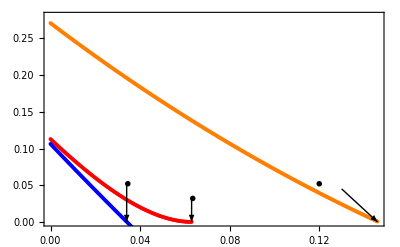

```mathematica
<<MaTeX`
ClearAll;(* Binary entropy function *)
h[x_] := Piecewise[{{-x Log2[x] - (1 - x) Log2[1 - x], 0 < x < 1}}, 0]

(* Nonlocal weight as function of disturbance D *)
pNL[d_] := √2(1 - 2 d) - 1
pL[d_] := 1 - pNL[d]

(* Effective error after preprocessing with flip prob q *)
eEff[q_, e_] := (1 - 2 q) e + q

(* Secret key rate as a function of D and q *)
r[d_, q_] := Module[{pl, e, ep},
  pl = pL[d];
  If[pl < 0 || pl > 1, Return[0]]; (* invalid region *)
  e = pl/4;  (* base error from pNL *)
  ep = (1 - 2 q) e + q;     (* post-processed error *)
  1 - h[ep] - pl/2(1 - h[q])
]
(*with preprocessing q*)
listd=Table[di,{di,0,0.063,.0005}];
(*rmax=NMaximize[{r[#,q],.5<=q<=1},q] &/@listd*) (*--uncomment to recalculate again*)
rmax={{0.112870741081322,{q->0.9824261952867979}},{0.11143612456023655,{q->0.9819805871553167}},{0.11000652560933433,{q->0.9815252315166674}},{0.1085819994971261,{q->0.9810599265602838}},{0.10716260222064,{q->0.9805844788219693}},{0.10574839051344231,{q->0.9800986817703685}},{0.10433942185380585,{q->0.9796023270800676}},{0.10293575447303249,{q->0.9790951967277592}},{0.10153744736392734,{q->0.9785770864495852}},{0.10014456028943075,{q->0.9780477587865548}},{0.09875715379141203,{q->0.9775069899860795}},{0.09737528919962701,{q->0.976954547728997}},{0.09599902864084497,{q->0.9763901919885724}},{0.094628435048143,{q->0.9758136786966292}},{0.0932635721703825,{q->0.9752247576663439}},{0.09190450458185695,{q->0.9746231728631418}},{0.09055129769212933,{q->0.974008661887688}},{0.08920401775605002,{q->0.9733809564157071}},{0.08786273188397353,{q->0.9727397793159589}},{0.0865275080521608,{q->0.9720848551363502}},{0.08519841511338988,{q->0.9714158888006507}},{0.08387552280776323,{q->0.9707325874143345}},{0.08255890177372716,{q->0.970034652802152}},{0.08124862355930262,{q->0.969321757155949}},{0.07994476063353306,{q->0.9685935992098104}},{0.0786473863981556,{q->0.967849846425475}},{0.07735657519949679,{q->0.967090163626029}},{0.07607240234060375,{q->0.9663142068887683}},{0.07479494409360965,{q->0.9655216212857822}},{0.07352427771234293,{q->0.964712049481374}},{0.07226048144518493,{q->0.9638851177817651}},{0.0710036345481787,{q->0.963040441197961}},{0.0697538172984008,{q->0.962177628652412}},{0.06851111100759477,{q->0.9612962827907}},{0.06727559803607663,{q->0.9603959753348343}},{0.06604736180691817,{q->0.9594762986838907}},{0.0648264868204127,{q->0.958536805790308}},{0.06361305866883327,{q->0.9575770563480059}},{0.06240716405148261,{q->0.9565965715895126}},{0.061208890790053205,{q->0.9555948813196588}},{0.060018327844291175,{q->0.954571501864358}},{0.05883556532798362,{q->0.9535259277498912}},{0.057660694525267675,{q->0.9524576244306023}},{0.05649380790727343,{q->0.9513660740569516}},{0.055334999149106445,{q->0.9502507125292976}},{0.05418436314718211,{q->0.9491109845127991}},{0.053041996036913064,{q->0.9479463070086354}},{0.0519079952107635,{q->0.9467560586958453}},{0.05078245933667924,{q->0.945539617893634}},{0.04966548837689844,{q->0.944296353755923}},{0.04855718360715622,{q->0.943025602757076}},{0.04745764763629057,{q->0.9417266648021946}},{0.04636698442626119,{q->0.9403988327896943}},{0.045285299312587624,{q->0.9390413909104104}},{0.04421269902522118,{q->0.937653559178585}},{0.04314929170986104,{q->0.9362345709948949}},{0.0420951869497197,{q->0.9347836160426478}},{0.0410504957877581,{q->0.9332998382655848}},{0.040015330749393674,{q->0.931782384625202}},{0.03898980586569989,{q->0.9302303550665342}},{0.03797403669710442,{q->0.9286428051713064}},{0.0369681403576021,{q->0.9270187693918086}},{0.035972235539493136,{q->0.9253572566130164}},{0.03498644253866379,{q->0.9236572008986916}},{0.03401088328041768,{q->0.9219175310068403}},{0.033045681345879374,{q->0.9201371262705685}},{0.03209096199897643,{q->0.9183148196862051}},{0.031146852214022136,{q->0.9164493789733215}},{0.0302134807039125,{q->0.9145395396901496}},{0.029290977948951524,{q->0.912583991005014}},{0.028379476226323197,{q->0.9105813368703229}},{0.02747910964022915,{q->0.9085301742191914}},{0.026590014152703234,{q->0.9064289664068771}},{0.025712327615131758,{q->0.9042761762146142}},{0.02484618980048614,{q->0.902070152163788}},{0.02399174243629887,{q->0.8998091874517824}},{0.023149129238392296,{q->0.8974914957572789}},{0.02231849594539026,{q->0.8951151852217534}},{0.021499990354027054,{q->0.8926782932798953}},{0.020693762355280088,{q->0.8901787502067224}},{0.019899963971346413,{q->0.8876143775795629}},{0.01911874939348812,{q->0.8849828959620442}},{0.01835027502077069,{q->0.882281917466364}},{0.017594699499718036,{q->0.8795088732949274}},{0.016852183764913597,{q->0.8766610985563432}},{0.0161228910805703,{q->0.8737357587022869}},{0.0154069870830984,{q->0.8707298780483651}},{0.014704639824703603,{q->0.8676402727380971}},{0.014016019818038017,{q->0.8644635631905216}},{0.013341300081941565,{q->0.8611962155911151}},{0.012680656188300055,{q->0.8578343951017819}},{0.012034266310057995,{q->0.8543740569091265}},{0.011402311270414689,{q->0.8508108619894617}},{0.010784974593243124,{q->0.8471402112078752}},{0.01018244255476597,{q->0.8433571088550453}},{0.009594904236525093,{q->0.8394562267920689}},{0.009022551579688565,{q->0.8354318432370785}},{0.008465579440728344,{q->0.8312777433197698}},{0.007924185648516602,{q->0.8269872292367091}},{0.007398571062881887,{q->0.8225530271103421}},{0.006888939634666746,{q->0.8179672179931621}},{0.006395498467340999,{q->0.8132211770844368}},{0.005918457880210171,{q->0.8083054010832122}},{0.005458031473275837,{q->0.803209508065737}},{0.005014436193795269,{q->0.7979219898929982}},{0.004587892404597338,{q->0.7924301026735552}},{0.004178623954207872,{q->0.7867196291059575}},{0.0037868582488447267,{q->0.7807746395874728}},{0.0034128263263401015,{q->0.7745772109644281}},{0.003056762932055035,{q->0.7681069550514361}},{0.0027189065968485915,{q->0.7613406069063922}},{0.002399499717169795,{q->0.7542513494918328}},{0.0020987886373424747,{q->0.7468079943957676}},{0.0018170237341164075,{q->0.7389738670138024}},{0.00155445950355515,{q->0.7307054247133611}},{0.0013113546503471518,{q->0.7219499931398713}},{0.0010879721796133168,{q->0.7126430945900877}},{0.0008845794913014959,{q->0.7027041316108723}},{0.0007014484772509544,{q->0.6920298170966375}},{0.0005388556210245143,{q->0.680484179764618}},{0.0003970821005961911,{q->0.6678813704400254}},{0.0002764138940003491,{q->0.6539550206732399}},{0.0001771418880391895,{q->0.6382981153515341}},{0.00009956199016158962,{q->0.6202268792307439}},{0.000043975243621319215,{q->0.5984086747710184}},{0.000010687946032428286,{q->0.5693775182259437}},{-9.103828801926284*^-15,{q->0.5000079205549213}}};
(*without preprocessing q*)
r0=r[#,0]&/@listd;
(*beyond quantum strategies*)
listd0=Table[di,{di,0,0.146,.0005}];
rmax0=1-h[pL[#]/2]/2-pL[#]/2&/@listd0;
{listd0,rmax0}ᵀ;
ListLinePlot[{{listd,rmaxᵀ[[1]]}ᵀ,{listd,r0}ᵀ,{listd0,rmax0}ᵀ},
Frame->{{True,True},{True,True}},FrameTicksStyle->Directive[Black,Thick],
FrameLabel->{MaTeX["D",Magnification->1.5],MaTeX["r",Magnification->1.5]},PlotRange->{0,0.28},
  PlotRangePadding -> None,
 PlotMarkers -> {"●", 4},PlotStyle -> {Red, Blue, Orange},
  PlotLegends -> Placed[
    SwatchLegend[
      {Red, Blue, Orange},
      {
        MaTeX["\\text{optimal}\\ q", Magnification -> 1],
        MaTeX["q=0", Magnification -> 1],
        MaTeX["\\text{beyond } \\mathcal{Q}", Magnification -> 1]
      }
    ],
    {Right, Top}
  ],
  Epilog -> {
    Arrow[{{0.063, 0.03}, {0.063, 0}}], Text[MaTeX["p_{\\mathrm{NL}} = 0.236", Magnification -> 1],{0.0635, 0.032},{-1, 0}],
    Arrow[{{0.034, 0.05}, {0.034, 0}}], Text[MaTeX["p_{\\mathrm{NL}} = 0.318", Magnification -> 1],{0.0345, 0.052},{-1, 0}],
    Arrow[{{0.13, 0.045}, {0.146, 0}}], Text[MaTeX["p_{\\mathrm{NL}} = 0", Magnification -> 1],{0.12, 0.052},{-1, 0}]
  }
 ]
```

### Security proof of CHSH Protocol (2006) - rates from enlarged Bell scenario

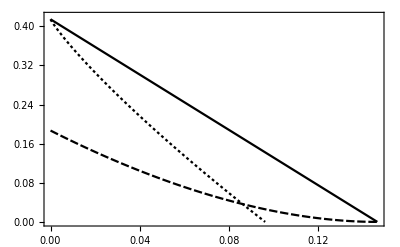

```mathematica
pNL[d_] := √2(1 - 2 d) - 1
pL[d_] := 1 - pNL[d]
(*the parameter p appears in Subscript[ρ, W]=pP_++(1-p)1/2, therefore to be compare with the disturbance d we use d=1-p*)
rNPJ06[p_]:=√2 p-1-h[(1+p)/2]
Plot[{pNL[d],(1-pL[d]/2)(1-h[pL[d]/(4-2 pL[d])]),rNPJ06[1-d]},{d,0,.1465},Frame->{{True,True},{True,True}},FrameTicksStyle->Directive[Black,Thick],
FrameLabel->{MaTeX["D",Magnification->1.5]," "},PlotRange->{0,0.42},
  PlotRangePadding -> None,PlotLegends -> Placed[
       {
        MaTeX["I_\\downarrow", Magnification -> 1],
        MaTeX["p_{\\mathrm{NL}}", Magnification -> 1],
        MaTeX["\\text{rate for (3,2)-CHAIN}", Magnification -> 1]
      }
    ,{Right, Top}
  ]]
```

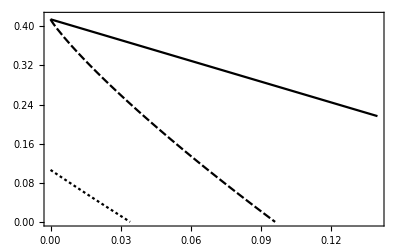

```mathematica
rNPJ06[p_]:=√2 p-1-h[(1+p)/2]
rNPJ06M[p_,M_]:=1-h[(1+p)/2]-M(1-p Cos[π/(2M)])
Plot[{(1+√2(1-p))-2,rNPJ06[1-p],r[p,0]},{p,0,0.14},Frame->True,FrameTicksStyle->Directive[Black,Thick],
FrameLabel->{MaTeX["1-\\nu",Magnification->1.5]," "},PlotRange->{0,0.42},
  PlotRangePadding -> None,PlotLegends -> Placed[
       {
        MaTeX["\\langle C\\rangle_\\rho-\\beta_{\\downarrow}", Magnification -> 1],
        MaTeX["r_{\\mathrm{chain}},\, M=2", Magnification -> 1],
        MaTeX["r_{\\mathrm{CHSH}},\, q=0", Magnification -> 1],
        MaTeX["r_{\\mathrm{chain}},", Magnification -> 1]
      }
    ,{0.8,0.3}]
    ]
```

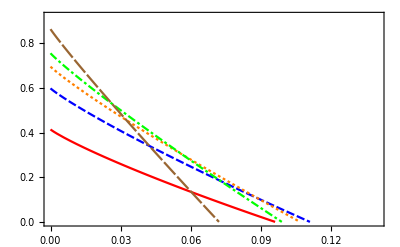

```mathematica
rNPJ06[p_]:=√2 p-1-h[(1+p)/2]
rNPJ06M[p_,M_]:=1-h[(1+p)/2]-M(1-p Cos[π/(2M)])
Plot[{rNPJ06M[1-p,2],rNPJ06M[1-p,3],rNPJ06M[1-p,4],rNPJ06M[1-p,5],rNPJ06M[1-p,9]},{p,0,0.14},PlotRange->{0,0.92},Frame->True,FrameTicksStyle->Directive[Black,Thick],
FrameLabel->{MaTeX["1-\\nu",Magnification->1.5],MaTeX["r",Magnification->1.5]},PlotStyle -> {Red, Blue, Orange,Green,Brown},
  PlotRangePadding -> None,PlotLegends -> Placed[
       {
        MaTeX["M=2", Magnification -> 1],
        MaTeX["M=3", Magnification -> 1],
        MaTeX["M=4", Magnification -> 1],
        MaTeX["M=5", Magnification -> 1],
        MaTeX["M=9", Magnification -> 1]
      }
    ,{0.8,0.6}]
    ]
```

### Device-Independent Security of Quantum Cryptography against Collective Attacks

A. Acín, N. Brunner, N. Gisin, S. Massar, S. Pironio, V. Scarani, “Device-Independent Security of Quantum Cryptography against Collective Attacks”, PRL 98, 230501 (2007)

S. Pironio, A. Acín, N. Brunner, N. Gisin, S. Massar, V. Scarani, “Device-independent quantum key distribution secure against collective attacks”, NJP 11 (2009) 04502 (2009)

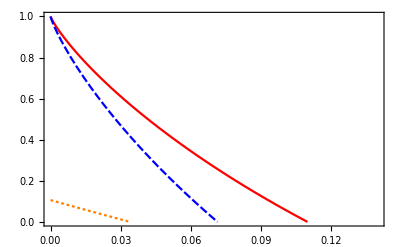

```mathematica
<<MaTeX``
  r[d_, q_] := Module[{pl, e, ep},
        pl = pL[d];
        If[pl < 0 || pl > 1, Return[0]]; (* invalid region *)
        e = pl/4;  (* base error from pNL *)
        ep = (1 - 2 q) e + q;     (* post-processed error *)
        1 - h[ep] - pl/2(1 - h[q])
]    
    rPRL07[Q_]:=Module[{h,β},
    h[x_] := Piecewise[{{-x Log2[x] - (1 - x) Log2[1 - x], 0 < x < 1}}, 0];
	β=2 √2(1-2Q);
	1-h[Q]-h[(1+√((β/2)^2-1))/2]
	]
	rBB84[Q_]:=Module[{β},
		β=2 √2(1-2Q);
		1-h[Q]-h[Q+β/(2 √2)]
		]
(*rNPJ06M[p_,M_]:=1-h[(1+p)/2]-M(1-p Cos[π/(2M)])
-Log2[(1+√(2-((2 √2(1-2Q))/2)^2))/2]
*)
Plot[{rBB84[Q],rPRL07[Q],r[Q,0]},{Q,0,0.14},PlotRange->{0,1},Frame->True,FrameTicksStyle->Directive[Black,Thick],
FrameLabel->{MaTeX["Q",Magnification->1.5],MaTeX["r",Magnification->1.5]},PlotStyle -> {Red, Blue, Orange,Green,Brown},
  PlotRangePadding -> None,PlotLegends -> Placed[
       {
        MaTeX["\\text{BB84}", Magnification -> 1],
        MaTeX["\\text{CHSH quant. col. attacks}", Magnification -> 1],
        MaTeX["\\text{CHSH no-signal attacks}", Magnification -> 1]     
      }
    ,{0.65,0.75}]
    ]
```

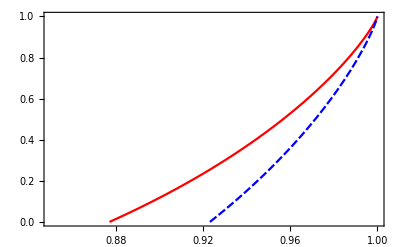

```mathematica
<<MaTeX``
    r[d_, q_] := Module[{pl, e, ep},
  pl = pL[d];
  If[pl < 0 || pl > 1, Return[0]]; (* invalid region *)
  e = pl/4;  (* base error from pNL *)
  ep = (1 - 2 q) e + q;     (* post-processed error *)
  1 - h[ep] - pl/2(1 - h[q])
]    
    rPRL07η[η_]:=Module[{h,Q,β},
    h[x_] := Piecewise[{{-x Log2[x] - (1 - x) Log2[1 - x], 0 < x < 1}}, 0];
	Q=η(1-η);
	β=2 √2 η^2+2(1-η)^2;
	1-h[Q]-h[(1+√((β/2)^2-1))/2]
	]
	rBB84η[η_]:=Module[{Q,β},
		Q=η(1-η);
		β=2 √2 η^2+2(1-η)^2;
		1-h[Q]-h[Q+β/(2 √2)]
		]
(*rNPJ06M[p_,M_]:=1-h[(1+p)/2]-M(1-p Cos[π/(2M)])
-Log2[(1+√(2-((2 √2(1-2Q))/2)^2))/2]
*)
Plot[{rBB84η[η],rPRL07η[η]},{η,.85,1},PlotRange->{0,1},Frame->True,FrameTicksStyle->Directive[Black,Thick],
FrameLabel->{MaTeX["\\eta",Magnification->1.5],MaTeX["r",Magnification->1.5]},PlotStyle -> {Red, Blue, Orange,Green,Brown},
  PlotRangePadding -> None,PlotLegends -> Placed[
       {
        MaTeX["\\text{BB84}", Magnification -> 1],
        MaTeX["\\text{CHSH quant. col. attacks}", Magnification -> 1],
        MaTeX["\\text{CHSH no-signal attacks}", Magnification -> 1]     
      }
    ,{0.35,0.75}]
    ]
```

Generalizations

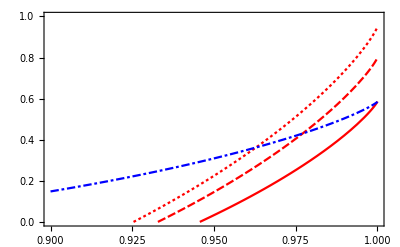

```mathematica
<<MaTeX``
   rPRL07ηq[η_,q_]:=Module[{h,Q,β},
    h[x_] := Piecewise[{{-x Log2[x] - (1 - x) Log2[1 - x], 0 < x < 1}}, 0];
	Q=η(1-η);
	β=2 √2 η^2+2(1-η)^2;
	1-h[Q]-q-(1-q)h[(1+√((β/2)^2-1))/2]
	]
	rPRL07ηqfake[η_,q_]:=Module[{h,Q,β},
    h[x_] := Piecewise[{{-x Log2[x] - (1 - x) Log2[1 - x], 0 < x < 1}}, 0];
	Q=η(1-η);
	β=4q+(1-q)2;
	1-h[Q]-q-(1-q)h[(1+√((β/2)^2-1))/2]
	]
(*rNPJ06M[p_,M_]:=1-h[(1+p)/2]-M(1-p Cos[π/(2M)])
-Log2[(1+√(2-((2 √2(1-2Q))/2)^2))/2]
*)
Plot[{rPRL07ηq[η,.414],rPRL07ηq[η,.2],rPRL07ηq[η,.05],rPRL07ηqfake[η,.414]},{η,.9,1},PlotRange->{0,1},
Frame->True,FrameTicksStyle->Directive[Black,Thick],
FrameLabel->{MaTeX["\\eta",Magnification->1.5],MaTeX["r",Magnification->1.5]},PlotStyle -> {Red, Red,Red,Blue},
  PlotRangePadding -> None,
  PlotLegends -> Placed[
       {
        MaTeX["p_g^M=\\sqrt{2}-1\,\\left(\\beta_\mathcal{Q}(\\hat{\\mathbf{p}})\\right)", Magnification -> 1],
        MaTeX["p_g^M=0.1\,\\left(\\beta_\mathcal{Q}(\\hat{\\mathbf{p}})\\right)", Magnification -> 1],
        MaTeX["p_g^M=0.05\,\\left(\\beta_\mathcal{Q}(\\hat{\\mathbf{p}})\\right)", Magnification -> 1],
        MaTeX["p_g^M=\\sqrt{2}-1\,\\left(\\beta_\mathcal{Q}^\\prime(\\mathbf{p})\\right)", Magnification -> 1]
        
      }
    ,{0.3,0.7}]
    ]
```

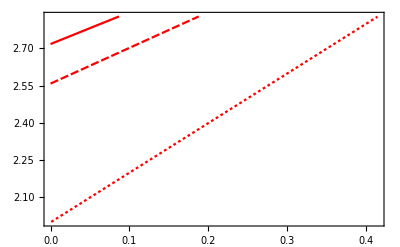

{{η→0},{η→2/(1+√2)}}

{2.71722,2.55766,1.99829}

```mathematica
β1[η_]:=2 √2 η^2+2(1-η)^2;
β2[q_,β0_]:=4q+(1-q)β0;
(*Plot[{2,β1[η],β2[0.4,2]},{η,0.828,1}]*)
Plot[{β2[q,β1[.98]],β2[q,β1[.95]],β2[q,β1[.828]]},{q,0,√2-1},PlotRange->{2,2 √2},
	Frame->True,FrameTicksStyle->Directive[Black,Thick],
	FrameLabel->{MaTeX["p_g^M",Magnification->1.5],MaTeX["\\beta^\\prime(\\mathbf{p})",Magnification->1.5]},PlotStyle -> {Red, Red,Red,Blue},
    PlotRangePadding -> None,
	PlotLegends -> Placed[
       {
        MaTeX["\\eta=.98,\\beta(\\hat{\\mathbf{p}})=2.71", Magnification -> 1],
        MaTeX["\\eta=.95,\\beta(\\hat{\\mathbf{p}})=2.56", Magnification -> 1],
        MaTeX["\\eta=2/(1+\\sqrt{2}),\\beta(\\hat{\\mathbf{p}})=2", Magnification -> 1]
      }
    ,{0.7,0.22}]]
Solve[β1[η]==2,η]
{β1[.98],β1[.95],β1[.828]}
```

Generalization 1 and 2 together from the section CHSH_χ. Note that the term h[(1+√(1-q(1-q)(8-β1^2)))/2] comes from [M. Ho, P. Sekatski, E.Y.-Z. Tan, R. Renner , J.-D. Bancal, N. Sangouard, “Noisy Preprocessing Facilitates a Photonic Realization of Device-Independent Quantum Key Distribution”, PRL 124, 230502 (2020)] obtained with EAT.

```mathematica
ClearAll;
rχ[η_,pgm_,q_,β_]:=Module[{h,χ,β1,β2,Q},
	h[x_] := Piecewise[{{-x Log2[x] - (1 - x) Log2[1 - x], 0 < x < 1}}, 0];
	χ[β0_]:=h[1/2+1/2 √((β0/2)^2-1)];
	Q=η(1-η);
	β1=4pgm+(1-pgm)2;
	β2=2 √2 η^2+2(1-η)^2;
	
	If[β==1,1-h[Q]-pgm-h[(1+√(1-q(1-q)(8-β1^2)))/2]-(1-pgm)χ[β1],1-h[Q]-pgm-h[(1+√(1-q(1-q)(8-β2^2)))/2]-(1-pgm)χ[β2]]
	]
	rχ[.99,0,0,1]
```

### Device-Independent Security of Quantum Cryptography against Coherent Attacks

L. Masanes, S. Pironio, A. Acín, “Secure device-independent quantum key distribution with causally independent measurement devices”, nATuRE COMMunICATIOnS | 2:238 (2011)

E. Hanggi, R. Renner, “Device-Independent Quantum Key Distribution with Commuting Measurements”, arXiv 2010

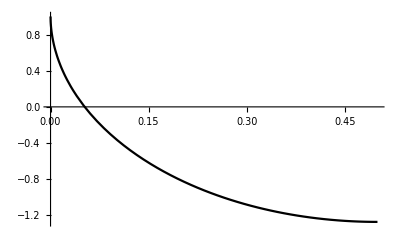

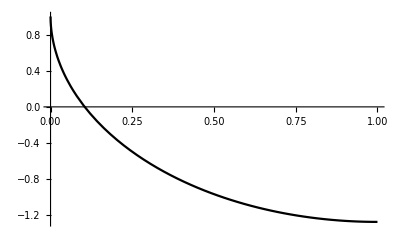

{{ν→-0.89555},{ν→0.89555}}

```mathematica
ClearAll;
rpg[Q_]:=Module[{h,β},
	h[x_] := Piecewise[{{-x Log2[x] - (1 - x) Log2[1 - x], 0 < x < 1}}, 0];
	β=2 √2(1-2Q);
	1-h[Q]-Log2[1+√(2-β^2/4)]
	]
	rpgν[ν_]:=Module[{h},
	h[x_] := Piecewise[{{-x Log2[x] - (1 - x) Log2[1 - x], 0 < x < 1}}, 0];
	1-h[(1-ν)/2]-Log2[1+√(2(1-ν^2))]
	]
	Plot[rpg[1-Q],{Q,0.,.5}]
	Plot[rpgν[1-ν],{ν,0.,1}]
	NSolve[rpgν[ν]==0,ν]
```

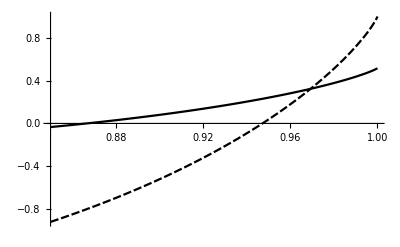

```mathematica
Plot[{rχ[η,0.4,0.9,1],rχ[η,0,0.9,2]},{η,0.85,1}]
```

### Device-Independent Quantum Key Distribution with Local Bell Test

C. Lim, C. Portmann, M. Tomamichel, R. Renner, N. Gisin, “Device-Independent Quantum Key Distribution with Local Bell Test”, PRX 3, 031006 (2013)

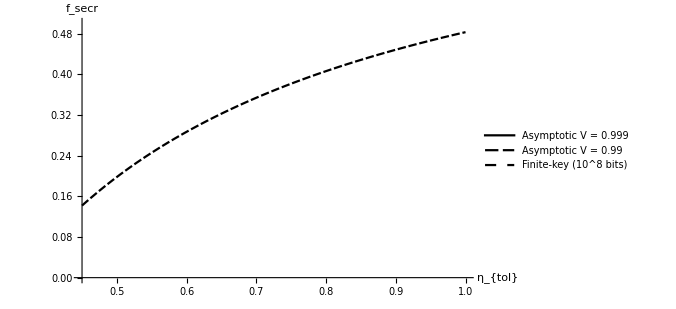

```mathematica
(* ---------- parameters ---------- *)
h[q_]  := -q Log[2, q] - (1 - q) Log[2, 1 - q];   (* binary entropy *)

Qtol   = 0.01;                       (* depolarising error rate     *)
etas   = {0.45, 1};                  (* plotting range for η_tol     *)

(* asymptotic secret-fraction, Eq. (2) *)
fAsym[S_, η_] := 1 - Log[2, 1 + (S/(4 η)) Sqrt[8 - S^2]] - 2 h[Qtol];

(* visibility settings used in the paper *)
vis     = {0.999, 0.99};
Svals   = 2 Sqrt[2] # &  /@ vis;     (* S = 2√2·V                  *)

(* finite-key approximation: parameters chosen exactly as in caption *)
fFinite[η_] := Module[{S = 2 Sqrt[2]}, 
  1 - Log[2, 1 + (S/(4 η)) Sqrt[8 - S^2]]         (* “log-term”         *)
    - 1.1 h[Qtol]                                 (* EC leakage (1.1×)  *)
    - h[Qtol]                                     (* privacy-amp term   *)
];

(* ---------- plotting ---------- *)
asymCurves = Table[fAsym[Svals[[k]], η], {k, 1, Length[vis]}];

Plot[
  Evaluate@Join[asymCurves, {fFinite[η]}],
  {η, Sequence @@ etas},
  PlotStyle -> {Thick, Thick, Dashed},
  PlotLegends -> {
      "Asymptotic  V = 0.999",
      "Asymptotic  V = 0.99",
      "Finite-key (10^8 bits)"
  },
  AxesLabel  -> {"η_{tol}", "\!\(\*SubscriptBox[\(f\), \(secr\)]\)"},
  PlotRange  -> {0, 0.5},
  ImageSize  -> 500
]
```

### CHSH_T-Noisy Preprocessing

### CH-SH protocol -- Splitting CHSH parameter estimation

P. Sekatski, J.-D. Bancal, X. Valcarce, E. Y.-Z. Tan, R. Renner, and N. Sangouard, Quantum 5, 444 (2021).
E. Woodhead, A. Ac.b4ın, and S. Pironio, Quantum 5, 443 (2021).

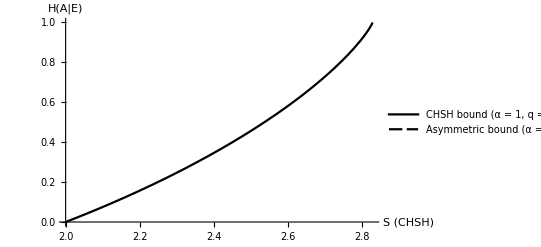

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

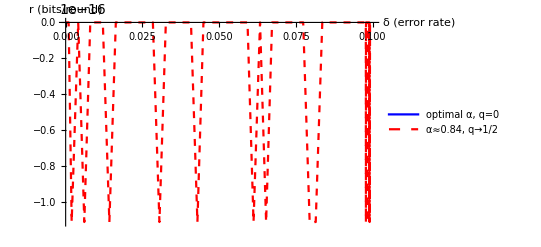

```mathematica
(* ::Section:: *)
(*DI-QKD – two recent analytic bounds*)

(* binary entropy *)
φ[x_] := -((1 + x)/2) Log2[(1 + x)/2] - ((1 - x)/2) Log2[(1 - x)/2];

(* 1) CHSH-only bound of Acín et al. 2006 *)
gCHSH[s_] := 1 - φ[Sqrt[(s/2)^2 - 1]];           (* H(A1|E) vs CHSH S,  q = 0 *)

(* 2) Asymmetric CHSH bound of Woodhead et al.
   \bar g_{q,α}(Sα) specialised to the convex branch |α|≥1    *)
gAlpha[s_, α_, q_] := Module[{x = Sqrt[s^2/4 - α^2]},
   1 + φ[Sqrt[(1 - 2 q)^2 + 4 q (1 - q) x^2]] - φ[x]
];

(* 3) Key-rate (Devetak-Winter) for depolarising channel, visibility v=1-2δ  *)
h[x_] := -x Log2[x] - (1 - x) Log2[1 - x];
keyRate[δ_, α_: 1, q_: 0] := Module[
  {Sα = Sqrt[2] (1 + α) (1 - 2 δ),
   δq = q + (1 - 2 q) δ},
  gAlpha[Sα, α, q] - h[δq]                     (* r ≥ ... bits per channel use *)
];

(* ::Section:: *)
(*Plots mirroring the main figures in both papers*)

(* A) Eve-entropy bound comparison *)
Plot[
 {gCHSH[s], gAlpha[s, 0.9, 0]}, {s, 2, 2 Sqrt[2]},
 AxesLabel -> {"S  (CHSH)", "H(A|E)"},
 PlotLegends -> {
   "CHSH bound (α = 1,  q = 0)",
   "Asymmetric bound (α = 0.9,  q = 0)"
 },
 PlotRange -> {0, 1}
]

(* B) Key-rate vs depolarising error (best α, with & w/o preprocessing) *)
rateNoPre = Plot[
  Evaluate@Table[
    keyRate[δ, α, 0] /. 
     α -> (1/(1 - 2 δ)) Max[1, Sqrt[(1 - 2 δ)^2/(1 - 2 δ)^2] - 1], 1],
  {δ, 0, 0.1},
  PlotStyle -> {Blue},
  PlotLegends -> {"optimal α, q=0"},
  AxesLabel -> {"δ  (error rate)", "r  (bits/round)"}
];

ratePre = Plot[
  keyRate[δ, 0.84, 1/2], {δ, 0, 0.1},
  PlotStyle -> {Red, Dashed},
  PlotLegends -> {"α≈0.84,  q→1/2"}
];

Show[rateNoPre, ratePre, PlotRange -> All]
```

### CHSH_(2e)-Double the events to generate the raw key bit

R. Schwonnek, K. T. Goh, I. W. Primaatmaja, E. Y.-Z. Tan, R. Wolf, V. Scarani, and C. C.-W. Lim, Nature communications 12, 2880 (2021).

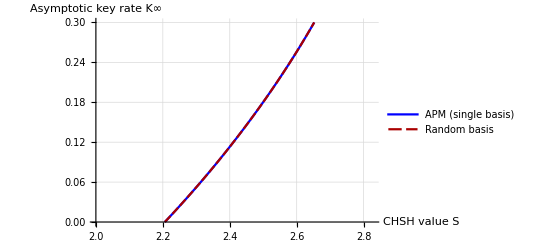

```mathematica
(* ::Section:: *)
(*Random-basis DIQKD – Asymptotic key-rate curves (Fig. 2 replica)*)

(* Binary entropy in bits *)
h2[p_?NumericQ] := If[p == 0 || p == 1, 0, -p Log2[p] - (1 - p) Log2[1 - p]];

(* Depolarising-noise QBER as a function of CHSH value S *)
qBER[S_?NumericQ] := (1/2) (1 - S/(2 Sqrt[2]));

(* Eve-uncertainty bound C*(S) – here we insert the tight linear approximation
   from Schwonnek et al.; replace with your favourite bound if desired         *)
Cstar[S_?NumericQ] := Log2[2] - h2[(1 + S/(2 Sqrt[2]))/2];

(* Secret-fraction r∞ and key-rate K∞ for the original APM protocol *)
rInfAPM[S_?NumericQ] := Cstar[S] - h2[qBER[S]];
KInfAPM[S_?NumericQ]  := (1/2) rInfAPM[S];          (* p = 1/2 gives ps = 1/2 *)

(* Random-basis protocol: choose λ=1/2 for S≤2.5, else λ=1               *)
lambda[S_] := If[S <= 2.5, 1/2, 1];               (* optimal per paper *)
rInfRB[S_?NumericQ] := Cstar[S] - h2[qBER[S]];    (* same Eve bound, different λ handled via p *)
KInfRB[S_?NumericQ]  := (1/2) rInfRB[S];

(* Plotting window *)
Smin = 2.0; Smax = 2 Sqrt[2];

Plot[{KInfAPM[S], KInfRB[S]}, {S, Smin, Smax},
 PlotStyle -> {Blue, Darker[Red]},
 PlotLegends -> {"APM (single basis)", "Random basis"},
 AxesLabel  -> {"CHSH value  S", "Asymptotic key rate  K∞"},
 PlotRange  -> {0, 0.30},
 ImageSize  -> 400,
 GridLines  -> Automatic]
```